```mathematica
(* result directory and load helpers*)
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"fourdiff.wl"
```

```mathematica
<<"inhom.wl"
```

```mathematica
dealias[f_,Nt_]:=Module[{},Re[√Nt InverseFourier[halve[1/(√(2Nt))Fourier[f],Nt]]]]
```

```mathematica
zeromode[f_]:=Module[{},Re[1/(√Length[f])Fourier[f]][[1]]]
```

### Load initial data

```mathematica
DeltaList={};
UpList={};
psicList={};
fcList={};
```

#### Collect Fortran data

```mathematica
resDir="FortranData";
data=Reverse[FileNames[resDir<>"/dim*/512"]];
```

```mathematica
(* collecting 512 mode results for Delta *)
Do[
dimNow=Import[data[[i]]<>"/shoot_inner.par","Table"][[2,1]]//Quiet;
DeltaNow=Import[data[[i]]<>"/Delta.out","Table"][[1,1]]//Quiet;
UpNow=Import[data[[i]]<>"/Up.out","Table"]//Flatten//Quiet;
psicNow=Import[data[[i]]<>"/psic.out","Table"]//Flatten//Quiet;
fcNow=Import[data[[i]]<>"/fc.out","Table"]//Flatten//Quiet;
tauList=Subdivide[DeltaNow,Length[UpNow]-1]//Quiet;
If[DeltaNow>0,
AppendTo[DeltaList,{dimNow,DeltaNow}];
AppendTo[UpList,Thread[{tauList[[;;]],UpNow[[;;]]}]];
AppendTo[psicList,Thread[{tauList[[;;]],psicNow[[;;]]}]];
AppendTo[fcList,Thread[{tauList[[;;]],fcNow[[;;]]}]];
(*Print[dimNow," ",DeltaNow]*)
]
,{i,Length[data]}]
```

#### Collect C++ data

```mathematica
resDir="CppData";
```

```mathematica
(*Import initial data from json files*)
json0=Import[resDir<>"/simulation_data_512.json"];
json1=Import[resDir<>"/data_lowD_1024_1.json"];
json2=Import[resDir<>"/data_lowD_1024_2.json"];
json3=Import[resDir<>"/data_lowD_1024_3.json"];
json4=Import[resDir<>"/data_lowD_1024_4.json"];
```

```mathematica
jsontot=Join[json0,json1,json2,json3,json4];
```

```mathematica
dims=jsontot[[;;,1]]//Sort//Reverse;
```

```mathematica
Do[
dimNow=dims[[i]];
initNow="Initial_Conditions"/.(dimNow/.jsontot);
DeltaNow="Delta"/.initNow;
(*Continue if entry not yet computed or duplicate*)
If[DeltaNow==0||MemberQ[DeltaList[[;;,1]],ToExpression[dimNow]],Continue[]];
UpNow="Up"/.initNow;
If[UpNow=={},Continue[]];
psicNow="psic"/.initNow;
fcNow="fc"/.initNow;
tauList=Subdivide[DeltaNow,Length[UpNow]-1]//Quiet;
If[DeltaNow>0,
AppendTo[DeltaList,{ToExpression[dimNow],DeltaNow}];
AppendTo[UpList,Thread[{tauList[[;;]],UpNow[[;;]]}]];
AppendTo[psicList,Thread[{tauList[[;;]],psicNow[[;;]]}]];
AppendTo[fcList,Thread[{tauList[[;;]],fcNow[[;;]]}]];
(*Print[dimNow," ",DeltaNow]*)
]
,{i,Length[dims]}]
```

### Compute a few other functions from boundary data

```mathematica
(*Pi and Psi are defined here like in the main paper, i.e. in terms of the numerical variables U and V they read 
Pi = √((D-2)^3/4)*(V+U)/(2x) and Psi = √((D-2)^3/4)*(V-U)/(2 x^2)*)
(*Omega is defined as (D-3)(e^ω-1)/x^2 *)
```

```mathematica
VpList={};
ia2pList={};
PipList={};
PsipList={};
omList={};
OmegapList={};
UcList={};
OmcList={};
PicList={};
```

```mathematica
Do[UpNow=UpList[[i,;;,2]];
fcNow=fcList[[i,;;,2]];
PsicNow=psicList[[i,;;,2]];
tauList=UpList[[i,;;,1]];
DeltaNow=DeltaList[[i,2]];
dimNow=DeltaList[[i,1]];
NtNow=Length[UpNow];
(*Compute ia2p*)
coeff1=3-dimNow-(dimNow-2)^3*UpNow^2/4;
coeff2=ConstantArray[dimNow-3,NtNow];
ia2pNow=solinhom[coeff1,coeff2,DeltaNow,NtNow];
AppendTo[ia2pList,Thread[{tauList[[;;]],ia2pNow[[;;]]}]];
AppendTo[omList,Thread[{tauList[[;;]],-Log[ia2pNow[[;;]]]}]];
(*Compute Vp*)
coeff1=(6-2*dimNow+(dimNow-2)*ia2pNow)/(2*ia2pNow);
coeff2=UpNow*(dimNow-2)/2;
VpNow=solinhom[coeff1,coeff2,DeltaNow,NtNow];
AppendTo[VpList,Thread[{tauList[[;;]],VpNow[[;;]]}]];
(*Compute Psip and Pip*)
AppendTo[PipList,Thread[{tauList[[;;]],√((dimNow-2)^3/4)(VpNow+UpNow)/2}]];
AppendTo[PsipList,Thread[{tauList[[;;]],√((dimNow-2)^3/4)(VpNow-UpNow)/2}]];
(*Compute Omegap*)
AppendTo[OmegapList,Thread[{tauList[[;;]],(dimNow-3)(1/ia2pNow[[;;]]-1)}]];
(*Compute u1c*)
coeff1=ConstantArray[1,NtNow];
coeff2=-(dimNow-1)PsicNow*fcNow;
u1cNow=solinhom[coeff1,coeff2,DeltaNow,NtNow];
(*Compute Pic and Omc; note that by construction Subscript[Ω, c] = (D-3)/(D-1)Subscript[Π, c]^2 *)
AppendTo[PicList,Thread[{tauList[[;;]],√((dimNow-2)^3/4)u1cNow}]];
AppendTo[OmcList,Thread[{tauList[[;;]],((dimNow-3)(dimNow-2)^3)/(4*(dimNow-1))u1cNow^2}]];
,{i,1,Length[DeltaList]}]
```

```mathematica
(* export to python *)
exportData={DeltaList,fcList,UcList,VpList,ia2pList,PsipList,PipList,PicList,OmcList};
```

```mathematica
tables=<|"Delta"->DeltaList,"fc"->fcList,"Uc"->UcList|>;
Export["boundaryData.json",tables,"JSON"];
```

```mathematica
(*Also compute some tau-derivatives*)
dtfcList={};
dtPicList={};
ddtPicList={};
```

```mathematica
Do[fcNow=fcList[[i,;;,2]];
PicNow=PicList[[i,;;,2]];
tauList=UpList[[i,;;,1]];
DeltaNow=DeltaList[[i,2]];
dimNow=DeltaList[[i,1]];
NtNow=Length[fcNow];
(*Compute tau-derivatives*)
dtfcNow=Re@fourdiff[fcNow,DeltaNow,NtNow];
dtPicNow=Re@fourdiff[PicNow,DeltaNow,NtNow];
ddtPicNow=Re@fourdiff[dtPicNow,DeltaNow,NtNow];
(*Assemble*)
AppendTo[dtfcList,Thread[{tauList[[;;]],dtfcNow}]];
AppendTo[dtPicList,Thread[{tauList[[;;]],dtPicNow}]];
AppendTo[ddtPicList,Thread[{tauList[[;;]],ddtPicNow}]];
,{i,1,Length[DeltaList]}]
```

```mathematica
(*compute ∂_y Subscript[Π, c]*)
dyPicList={};
Pi2csymb=√((dim-2)^3/4)( (128 (-1+dim^2) (Subscript[f0, 0][t])^5 Subscript[u0, 1][t]-16 (-2+dim)^3 (3-dim-3 dim^2+dim^3) (Subscript[f0, 0][t])^7 (Subscript[u0, 1][t])^3-64 (-1+dim^2) (Subscript[f0, 0][t])^4 Subscript[u0, 1][t] Subscript[f0, 0]'[t]-64 (-1+dim) (1+dim) (Subscript[f0, 0][t])^4 Subscript[f0, 0]'[t] Subscript[u0, 1]'[t]+64 (-1+dim^2) (Subscript[f0, 0][t])^5 (3 Subscript[u0, 1]'[t]+Subscript[u0, 1]''[t])))/(128 (-1+dim)^2 (1+dim) (Subscript[f0, 0][t])^7);
```

```mathematica
Do[fcNow=fcList[[i,;;,2]];
dtfcNow=dtfcList[[i,;;,2]];
PicNow=PicList[[i,;;,2]];
dtPicNow=dtPicList[[i,;;,2]];
ddtPicNow=ddtPicList[[i,;;,2]];
tauList=UpList[[i,;;,1]];
DeltaNow=DeltaList[[i,2]];
dimNow=DeltaList[[i,1]];
NtNow=Length[fcNow];
(*Assemble*)
dyPicNow=Pi2csymb/.{dim->dimNow,Subscript[f0, 0][t]->fcNow,Subscript[u0, 1][t]->√(4/(dimNow-2)^3)PicNow,Subscript[f0, 0]'[t]->dtfcNow,Subscript[u0, 1]'[t]->√(4/(dimNow-2)^3)dtPicNow,Subscript[u0, 1]''[t]->√(4/(dimNow-2)^3)ddtPicNow};
AppendTo[dyPicList,Thread[{tauList[[;;]],dyPicNow}]];
,{i,1,Length[DeltaList]}]
```

### DeltaPlot

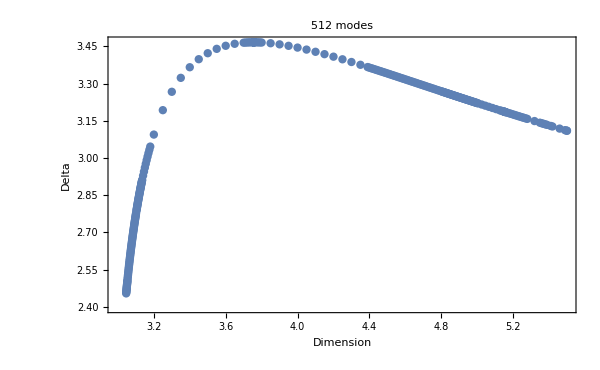

```mathematica
p1=ListPlot[DeltaList,Frame->True,FrameLabel->{"Dimension","Delta"},BaseStyle->{PointSize[0.01],Thick,16},ImageSize->600,PlotLabel->"512 modes"]
```

```mathematica
Export["DeltaList.dat",DeltaList]
```

DeltaList.dat

### GammaPlot

```mathematica
(*So far only Fortran results available, i.e. until D=3.1*)
```

```mathematica
resDir="FortranData";
```

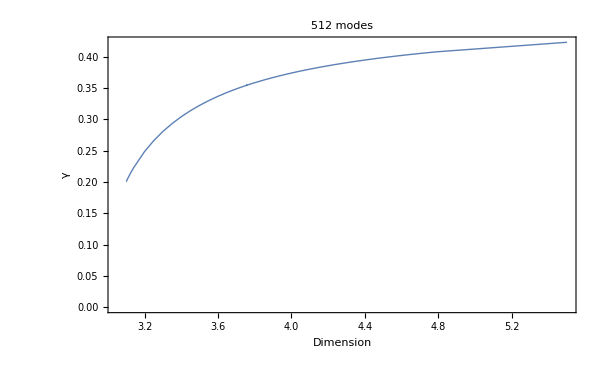

```mathematica
(* collecting 512 mode results for gamma *)
gam512=FileNames[resDir<>"/dim*/512"];
GammaList512={};
Do[
dimNow=Import[gam512[[i]]<>"/shoot_inner.par","Table"][[2,1]]//Quiet;
GammaNow=Import[gam512[[i]]<>"/gam.out","Table"][[1,1]]//Quiet;
If[GammaNow>0,AppendTo[GammaList512,{dimNow,GammaNow}];
(*Print[dimNow," ",DeltaNow]*)
]
,{i,Length[gam512]}]
p1=ListPlot[GammaList512,Frame->True,FrameLabel->{"Dimension","γ"},BaseStyle->{PointSize[0.01],Thick,16},ImageSize->600,PlotLabel->"512 modes",Joined->True]
```

```mathematica
Export["GammaList.dat",GammaList512]
```

GammaList.dat

```mathematica
gampoly[dim_]=((dim-3)^a+b)/.FindFit[GammaList512,(dim-3)^a+b,{a,b},dim]
```

-0.631756+(-3+dim)^0.0782934

```mathematica
gampoly2[dim_]=(a/(dim-3)+b)/.FindFit[GammaList512,a/(dim-3)+b,{a,b},dim]
```

0.400531-0.022603/(-3+dim)

```mathematica
gamlog[dim_]=(a*Log10[(dim-3)/dim]+b)/.FindFit[GammaList512,a*Log10[(dim-3)/dim]+b,{a,b},dim]
```

0.492514+0.0860897 Log[(-3+dim)/dim]

```mathematica
gamexp[dim_]=(a-b*Exp[-c*dim])/.FindFit[GammaList512,a-b*Exp[-c*dim],{a,b,c},dim]
```

0.41331-88.1036 ⅇ^(-1.94985 dim)

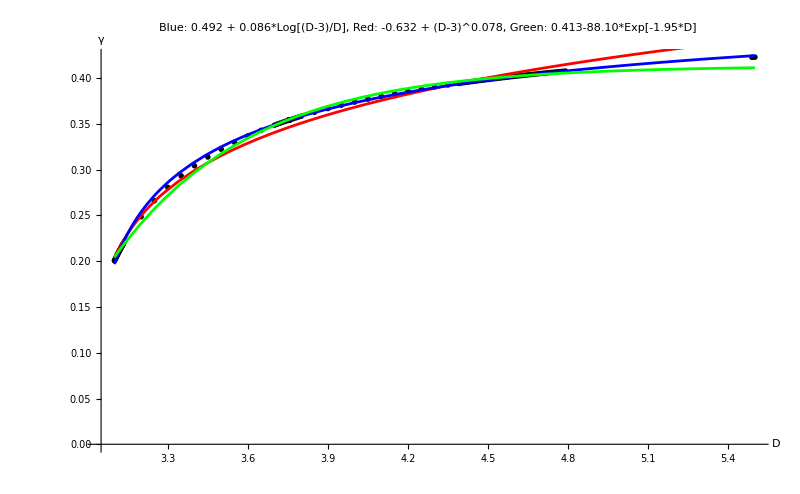

```mathematica
Show[{ListPlot[GammaList512,PlotLabel->"Blue: 0.492 + 0.086*Log[(D-3)/D], Red: -0.632 + (D-3)^0.078, Green: 0.413-88.10*Exp[-1.95*D]",AxesLabel->{"D","γ"},PlotStyle->{Black,PointSize[0.005]},BaseStyle->15],Plot[gampoly[dim],{dim,3.1,5.5},PlotStyle->{Red},PlotRange->All],Plot[gamlog[dim],{dim,3.1,5.5},PlotStyle->{Blue},PlotRange->All],Plot[gamexp[dim],{dim,3.1,5.5},PlotStyle->{Green},PlotRange->All]},ImageSize->800]
```

## Various plots over D for analytics

```mathematica
dimList=DeltaList[[;;,1]];
```

```mathematica
ColorList=Table[ColorData["Rainbow",j/(Length[dimList]-1)],{j,0,Length[dimList]-1}];
```

```mathematica
(*Check identity*)
Max[Abs[OmcList[[10,;;,2]]-(dimList[[10]]-3)/(dimList[[10]]-1)PicList[[10,;;,2]]^2]]
```

7.10543×10^-15

### Zero mode of Ω at SSH

```mathematica
Ωpzero=Table[{dimList[[i]],zeromode[OmegapList[[i,;;,2]]]},{i,1,Length[dimList]}];
```

```mathematica
Ωpzerofit[x_]:=(a*(x-3)^b)/.FindFit[Ωpzero[[-50;;]],a*(dim-3)^b,{a,b},dim]
```

```mathematica
Ωpzerofit[x]
```

0.399086 (-3+x)^0.081691

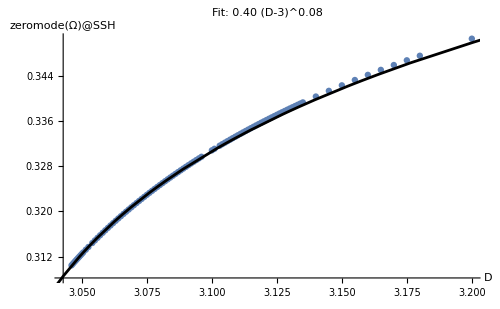

```mathematica
Show[{ListPlot[Ωpzero[[-100;;]],AxesLabel->{"D","zeromode(Ω)@SSH"},PlotLabel->"Fit: 0.40 (D-3)^0.08",ImageSize->500,BaseStyle->16],Plot[Ωpzerofit[x],{x,3,5.5},PlotStyle->Black]}]
```

```mathematica
Omzeropint=Interpolation[Ωpzero];
```

```mathematica
dOmzeroint[x_]=D[Omzeropint[x],x];
```

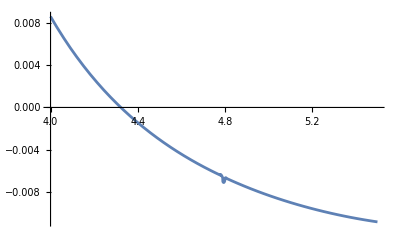

```mathematica
Plot[dOmzeroint[x],{x,4,5.5}]
```

### Zero mode of ω at SSH

```mathematica
ompzero=Table[{dimList[[i]],zeromode[omList[[i,;;,2]]]},{i,1,Length[dimList]}];
```

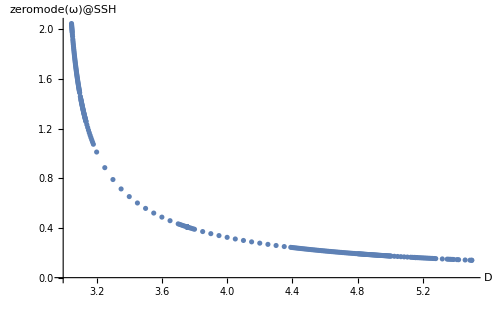

```mathematica
ListPlot[ompzero[[;;]],AxesLabel->{"D","zeromode(ω)@SSH"},ImageSize->500,BaseStyle->16]
```

```mathematica
omzeropint=Interpolation[ompzero];
```

```mathematica
domzeroint[x_]=D[omzeropint[x],x];
```

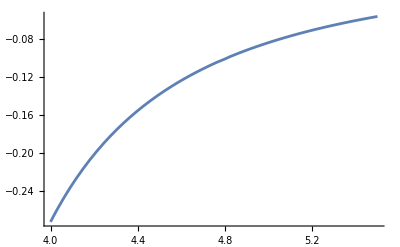

```mathematica
Plot[domzeroint[x],{x,4,5.5}]
```

### Zero mode of f at center

```mathematica
fczero=Table[{dimList[[i]],zeromode[fcList[[i,;;,2]]]},{i,1,Length[dimList]}];
```

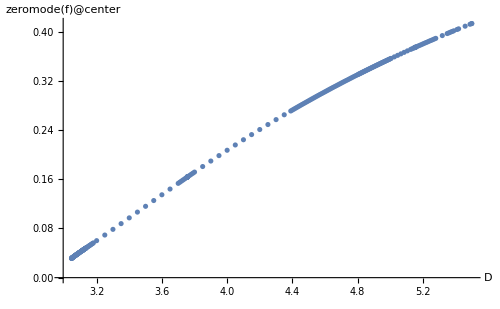

```mathematica
ListPlot[fczero,AxesLabel->{"D","zeromode(f)@center"},ImageSize->500,BaseStyle->16]
```

```mathematica
fczeroint=Interpolation[fczero,InterpolationOrder->3]
```

InterpolatingFunction[…]

```mathematica
dfczeroint[x_]=D[fczeroint[x],x];
ddfczeroint[x_]=D[fczeroint[x],{x,2}];
```

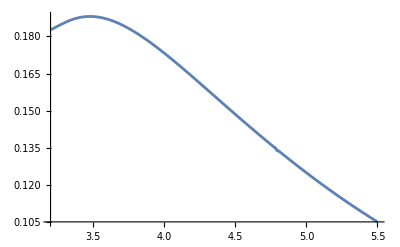

```mathematica
Plot[dfczeroint[x],{x,3.2,5.5}]
```

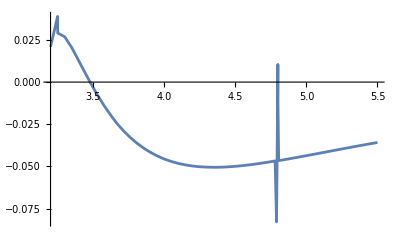

```mathematica
Plot[ddfczeroint[x],{x,3.2,5.5}]
```

```mathematica
FindRoot[ddfczeroint[x],{x,3.5}]
```

{x→3.47799}

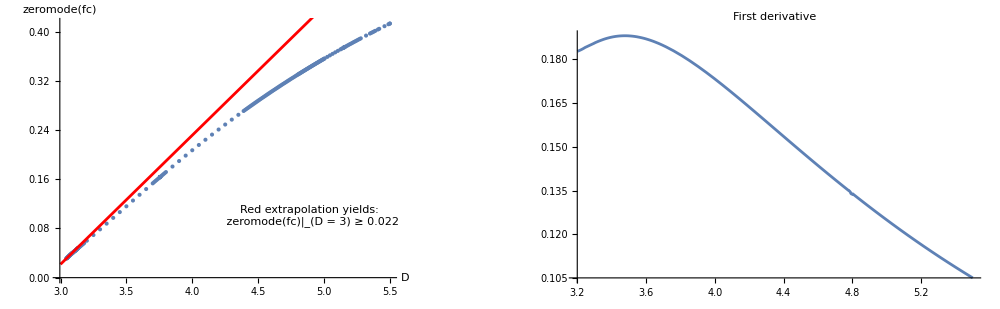

```mathematica
GraphicsRow[{Show[ListPlot[fczero,AxesLabel->{"D","zeromode(fc)"},BaseStyle->16,Epilog->Inset["Red extrapolation yields: \n zeromode(fc)|_(D = 3) ≥ 0.022",{4.9,0.1}]],Plot[-0.6078164628904656+0.20984523981144285 x,{x,3,5.5},PlotStyle->Red]],Plot[dfczeroint[x],{x,3.2,5.5},PlotLabel->"First derivative",Epilog->Inset["Inflection point at D = 3.478",{3.55,0.191}]]},ImageSize->1000]
```

```mathematica
linearextrap[x_]=(a*x+b)/.FindFit[fczero[[-2;;]],a*x+b,{a,b},x]
```

-0.607816+0.209845 x

```mathematica
linearextrap[3]
```

0.0217193

### Minimum of f at center

```mathematica
fcmin=Table[{dimList[[i]],Min[fcList[[i,;;,2]]]},{i,1,Length[dimList]}];
```

```mathematica
Clear[fcminfit]
```

```mathematica
fcminfit[x_]=(a*x+b)/.FindFit[fcmin[[-100;;]],{a*x+b},{a,b},x]
```

-0.300716+0.102697 x

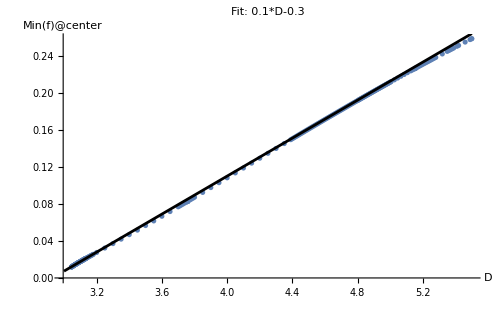

```mathematica
Show[{ListPlot[fcmin,AxesLabel->{"D","Min(f)@center"},ImageSize->500,BaseStyle->16,PlotLabel->"Fit: 0.1*D-0.3"],Plot[fcminfit[x],{x,3,5.5},PlotStyle->Black]}]
```

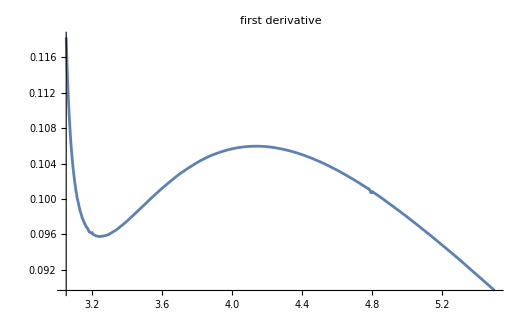
```mathematica
-Graphics--Graphics-
```

-Graphics- -Graphics-

```mathematica
fcminint=Interpolation[fcmin,InterpolationOrder->3]
```

InterpolatingFunction[…]

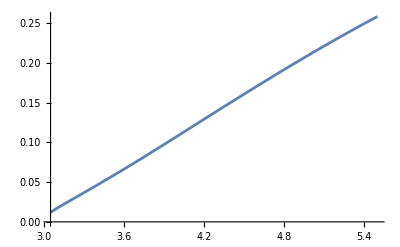

```mathematica
Plot[fcminint[x],{x,3.046,5.5}]
```

```mathematica
dfcminint[x_]=D[fcminint[x],x];
```

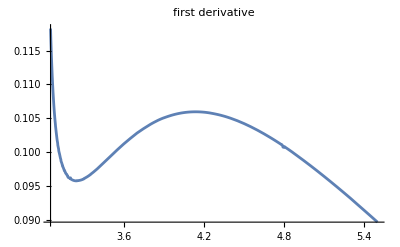

```mathematica
Plot[dfcminint[x],{x,3.05,5.5},PlotLabel->"first derivative",BaseStyle->16]
```

### Zero mode of Ω at center

```mathematica
Ωczero=Table[{dimList[[i]],zeromode[OmcList[[i,;;,2]]]},{i,1,Length[dimList]}];
```

```mathematica
Ωczerofit[x_]:=(a*(x-3)^b)/.FindFit[Ωczero[[-50;;]],a*(dim-3)^b,{a,b},dim]
```

```mathematica
Ωczerofit[x]
```

539.496/(-3+x)^0.349805

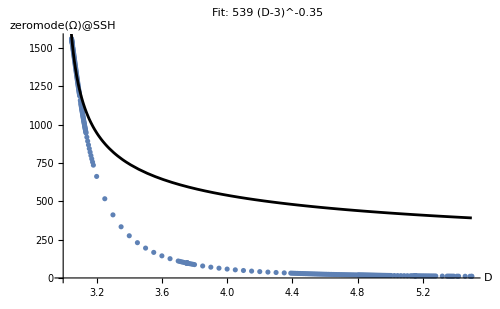

```mathematica
Show[{ListPlot[Ωczero[[;;]],AxesLabel->{"D","zeromode(Ω)@SSH"},PlotLabel->"Fit: 539 (D-3)^-0.35",ImageSize->500,BaseStyle->16],Plot[Ωczerofit[x],{x,3,5.5},PlotStyle->Black,PlotRange->All]}]
```

```mathematica
Omzerocint=Interpolation[Ωczero];
```

```mathematica
dOmzerocint[x_]=D[Omzerocint[x],x];
```

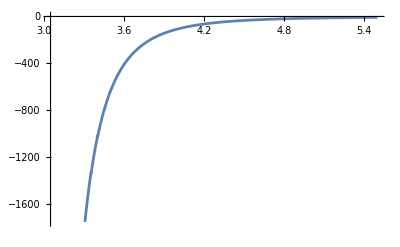

```mathematica
Plot[dOmzerocint[x],{x,3.046,5.5}]
```

### Zero mode of Π_c^2 at center

```mathematica
picsquzero=Table[{dimList[[i]],zeromode[(PicList[[i,;;,2]])^2]},{i,1,Length[dimList]}];
```

```mathematica
picsquzerofit[x_]:=(a*(x-3)^b)/.FindFit[picsquzero[[-50;;]],a*(dim-3)^b,{a,b},dim]
```

```mathematica
picsquzerofit[x]
```

1260.5/(-3+x)^1.3052

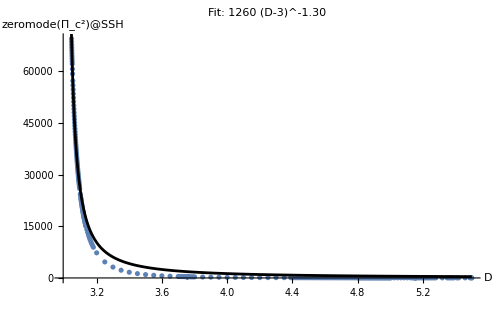

```mathematica
Show[{ListPlot[picsquzero[[;;]],AxesLabel->{"D","zeromode(Π_c^2)@SSH"},PlotLabel->"Fit: 1260 (D-3)^-1.30",ImageSize->500,BaseStyle->16],Plot[picsquzerofit[x],{x,3,5.5},PlotStyle->Black,PlotRange->All]}]
```

### Minimum of Ω at center

```mathematica
Ωcmin={};
```

```mathematica
Do[OmcNow=Interpolation[OmcList[[i]]];
min=FindMinimum[OmcNow[tau],{tau,0.4}][[2]]//Quiet;
tauval=tau/.min;
AppendTo[Ωcmin,{dimList[[i]],tauval}];
Clear[OmcNow,min];
,{i,1,Length[dimList]}]
```

```mathematica
(*Do[imin=Position[OmcList[[i,;;,2]],Min[OmcList[[i,;;,2]]]][[1,1]];
tauval=OmcList[[i,imin,1]];
AppendTo[Ωcmin,{dimList[[i]],tauval}],{i,1,Length[dimList]}]*)
```

```mathematica
Ωcminfit[x_]:=(a*(x-3)^b)/.FindFit[Ωcmin[[-50;;]],a*(dim-3)^b,{a,b},dim]
```

```mathematica
Ωcminfit[x]
```

0.141935 (-3+x)^0.123297

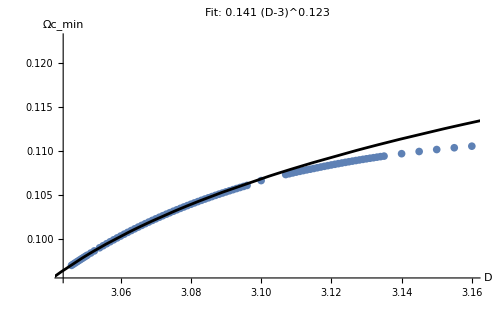

```mathematica
Show[{ListPlot[Ωcmin[[-95;;]],AxesLabel->{"D","Ωc_min"},PlotLabel->"Fit: 0.141 (D-3)^0.123",ImageSize->500,BaseStyle->16],Plot[Ωcminfit[x],{x,3,5.5},PlotStyle->Black,PlotRange->All]}]
```

```mathematica
Omminint=Interpolation[Ωcmin[[-95;;]]];
```

```mathematica
dOmminint[x_]=D[Omminint[x],x];
```

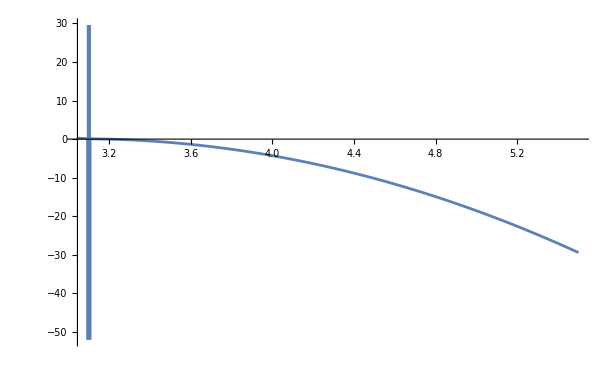

```mathematica
Plot[dOmminint[x],{x,3.046,5.5}]
```

### t=0 value of Π_c

```mathematica
pic0=Table[{dimList[[i]],PicList[[i,1,2]]},{i,1,Length[dimList]}];
```

```mathematica
pic0fit[x_]:=(a*(x-3)^b)/.FindFit[pic0[[-30;;]],a*(dim-3)^b,{a,b},dim]
```

```mathematica
pic0fit[x]
```

25.6342/(-3+x)^0.506114

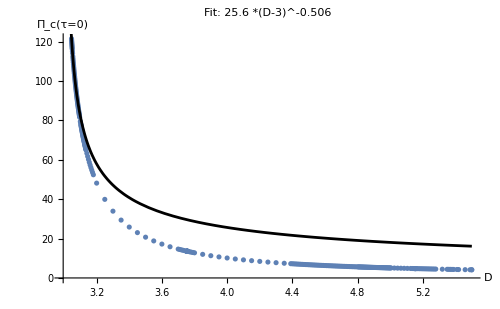

```mathematica
Show[{ListPlot[pic0,AxesLabel->{"D","Π_c(τ=0)"},PlotLabel->"Fit: 25.6 *(D-3)^-0.506",ImageSize->500,BaseStyle->16],Plot[pic0fit[x],{x,3.01,5.5},PlotStyle->Black,PlotRange->All]}]
```

### Local maxima of Ω_c

```mathematica
LocalMaxValues[data_List]:=Module[{triples,maxima},triples=Partition[data,3,1];(*overlapping triples {{p1,p2,p3},...}*)maxima=Cases[triples,{{x1_,y1_},{x2_,y2_},{x3_,y3_}}/;y2>y1&&y2>y3:>y2];
maxima];
```

```mathematica
locmax1=Table[{dimList[[i]],LocalMaxValues[OmcList[[i]]][[1]]},{i,1,Length[dimList]}];
```

```mathematica
locmax2=Table[{dimList[[i]],LocalMaxValues[OmcList[[i]]][[2]]},{i,1,Length[dimList]}];
```

```mathematica
ratio=Table[{dimList[[i]],LocalMaxValues[OmcList[[i]]][[1]]/LocalMaxValues[OmcList[[i]]][[2]]},{i,1,Length[dimList]}];
```

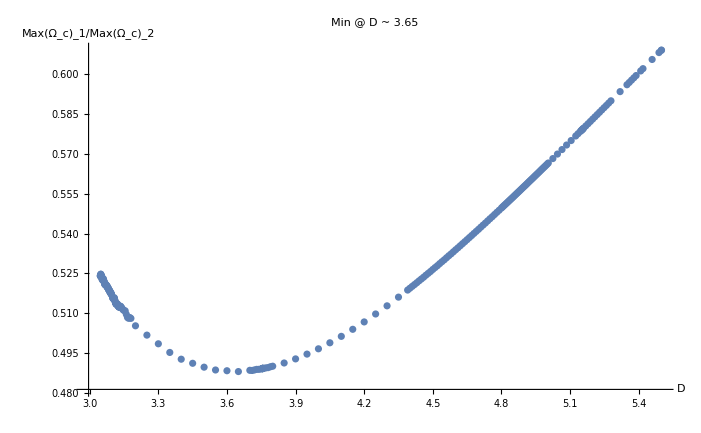

```mathematica
ListPlot[ratio,BaseStyle->16,AxesLabel->{"D","Max(Ω_c)_1/Max(Ω_c)_2"},PlotLabel->"Min @ D ~ 3.65"]
```

```mathematica
Position[ratio[[;;,2]],Min[ratio[[;;,2]]]][[1,1]]
```

159

```mathematica
ratio[[%]]
```

{3.65,0.488035}

### Power spectrum of f at center

```mathematica
nmodes=28;
```

```mathematica
(*modes to take*)
modes=Table[j,{j,1,nmodes,2}]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27}

```mathematica
modelabels=Table["Abs(fc_"<>ToString[j-1]<>")",{j,1,nmodes,2}]
```

{Abs(fc_0),Abs(fc_2),Abs(fc_4),Abs(fc_6),Abs(fc_8),Abs(fc_10),Abs(fc_12),Abs(fc_14),Abs(fc_16),Abs(fc_18),Abs(fc_20),Abs(fc_22),Abs(fc_24),Abs(fc_26)}

```mathematica
ColorListmodes=Table[ColorData["Rainbow",j/(Length[modes]-1)],{j,0,Length[modes]-1}];
```

```mathematica
fcpowerList=Table[{dimList[[i]],1/(√Length[fcList[[i]]])Abs[Fourier[fcList[[i,;;,2]]][[j]]]},{j,1,nmodes,2},{i,1,Length[dimList]}];
```

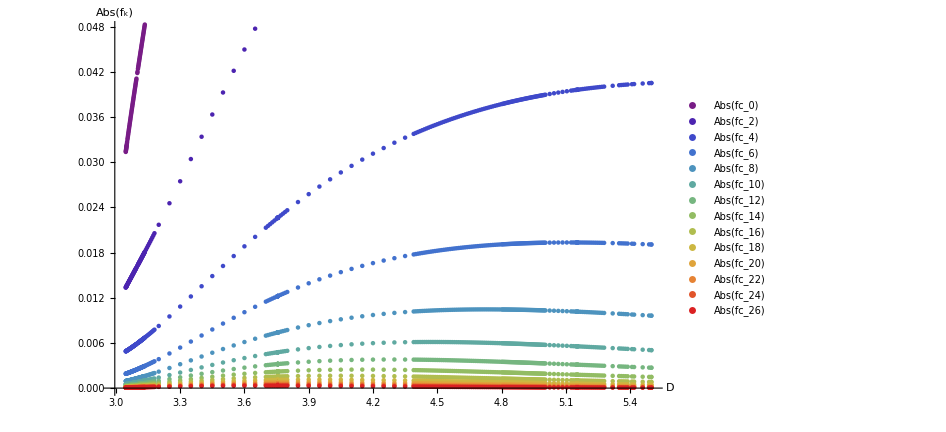

```mathematica
ListPlot[fcpowerList,PlotStyle->ColorListmodes,PlotLegends->modelabels,AxesLabel->{"D","Abs(f_k)"},ImageSize->700,BaseStyle->16]
```

### Power spectrum of Π_p

```mathematica
nmodes=9;
```

```mathematica
(*modes to take*)
modes=Table[j,{j,1,nmodes,2}]
```

{1,3,5,7,9}

```mathematica
modelabels=Table["k="<>ToString[j-1],{j,2,nmodes,2}]
```

{k=1,k=3,k=5,k=7}

```mathematica
ColorListmodes=Table[ColorData["Rainbow",j/(Length[modes]-1)],{j,0,Length[modes]-1}];
```

```mathematica
PipimList=Table[{dimList[[i]],1/(√Length[PipList[[i]]])Im[Fourier[PipList[[i,;;,2]]][[j]]]},{j,2,nmodes,2},{i,1,Length[dimList]}];
```

```mathematica
PipreList=Table[{dimList[[i]],1/(√Length[PipList[[i]]])Re[Fourier[PipList[[i,;;,2]]][[j]]]},{j,2,nmodes,2},{i,1,Length[dimList]}];
```

```mathematica
PipreList//Dimensions
```

{4,267,2}

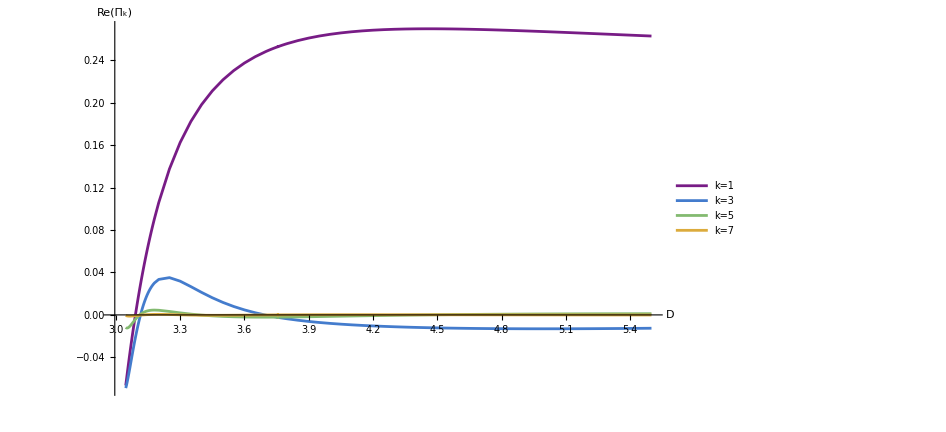
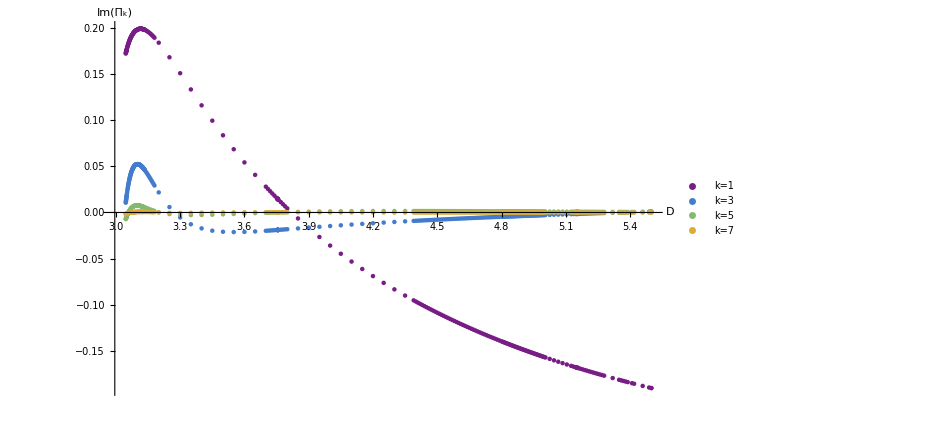

```mathematica
{ListPlot[PipreList,PlotStyle->ColorListmodes,PlotLegends->modelabels,AxesLabel->{"D","Re(Π_k)"},ImageSize->700,BaseStyle->16,PlotRange->All,Joined->True],ListPlot[PipimList,PlotStyle->ColorListmodes,PlotLegends->modelabels,AxesLabel->{"D","Im(Π_k)"},ImageSize->700,BaseStyle->16,PlotRange->All]}
```

#### Check real parts

```mathematica
pip1=Interpolation[PipreList[[1]]];
```

```mathematica
dpip1[x_]=D[pip1[x],x];
```

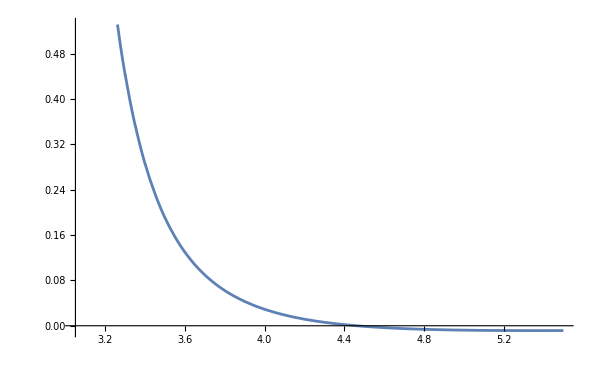

```mathematica
Plot[dpip1[x],{x,3.05,5.5}]
```

```mathematica
FindRoot[dpip1[x],{x,5}]
```

{x→4.46135}

```mathematica
pip3=Interpolation[PipreList[[2]]];
```

```mathematica
dpip3[x_]=D[pip3[x],x];
```

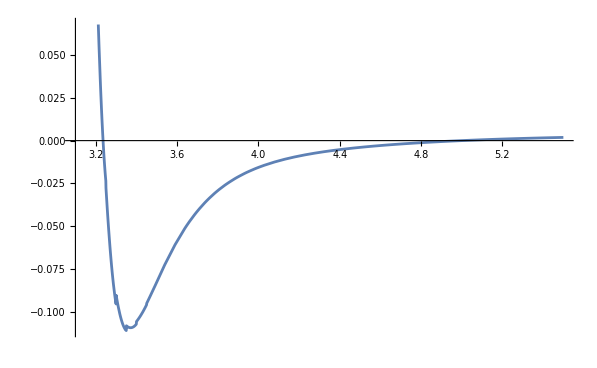

```mathematica
Plot[dpip3[x],{x,3.1,5.5}]
```

```mathematica
FindRoot[dpip3[x],{x,5}]
```

{x→4.99928}

```mathematica
pip5=Interpolation[PipreList[[3]]];
```

```mathematica
dpip5[x_]=D[pip5[x],x];
```

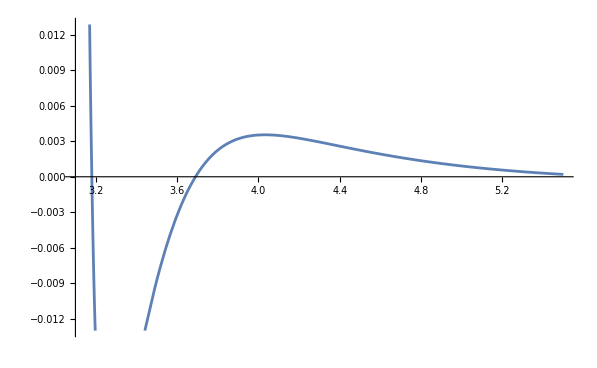

```mathematica
Plot[dpip5[x],{x,3.1,5.5}]
```

```mathematica
FindRoot[dpip5[x],{x,3.7}]
```

{x→3.69067}

### Power spectrum of Π_c

```mathematica
nmodes=18;
```

```mathematica
(*modes to take*)
modes=Table[j,{j,1,nmodes,2}]
```

{1,3,5,7,9,11,13,15,17}

```mathematica
modelabels=Table["k="<>ToString[j-1],{j,2,nmodes,2}]
```

{k=1,k=3,k=5,k=7,k=9,k=11,k=13,k=15,k=17}

```mathematica
ColorListmodes=Table[ColorData["Rainbow",j/(Length[modes]-1)],{j,0,Length[modes]-1}];
```

```mathematica
PicimList=Table[{dimList[[i]],1/(√Length[PicList[[i]]])Im[Fourier[PicList[[i,;;,2]]][[j]]]},{j,2,nmodes,2},{i,1,Length[dimList]}];
```

```mathematica
PicreList=Table[{dimList[[i]],1/(√Length[PicList[[i]]])Re[Fourier[PicList[[i,;;,2]]][[j]]]},{j,2,nmodes,2},{i,1,Length[dimList]}];
```

```mathematica
PicreList[[;;,1]]
```

{{5.5,2.32231},{5.5,-0.0260282},{5.5,-0.391788},{5.5,0.188206},{5.5,0.0205017},{5.5,-0.0655363},{5.5,0.0250191},{5.5,0.00875421},{5.5,-0.012361}}

```mathematica
PicimList[[;;,1]]
```

{{5.5,-1.74314},{5.5,0.967731},{5.5,-0.217517},{5.5,-0.131963},{5.5,0.121784},{5.5,-0.0184792},{5.5,-0.0288193},{5.5,0.0197828},{5.5,-0.000273439}}

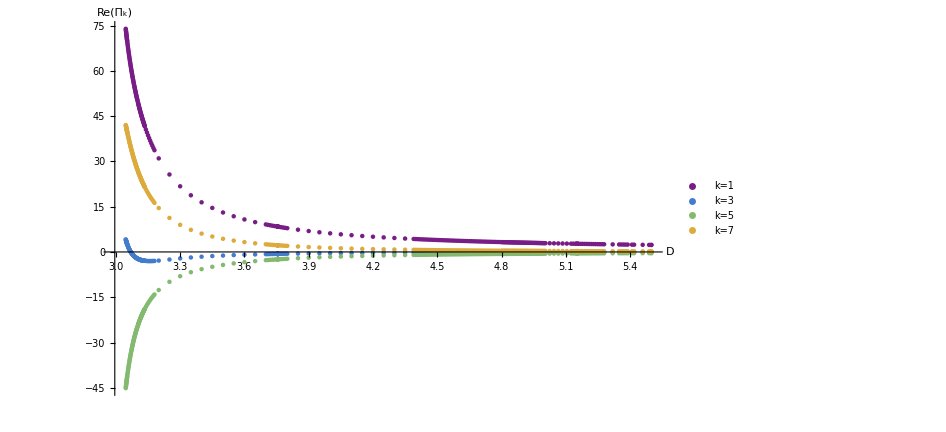
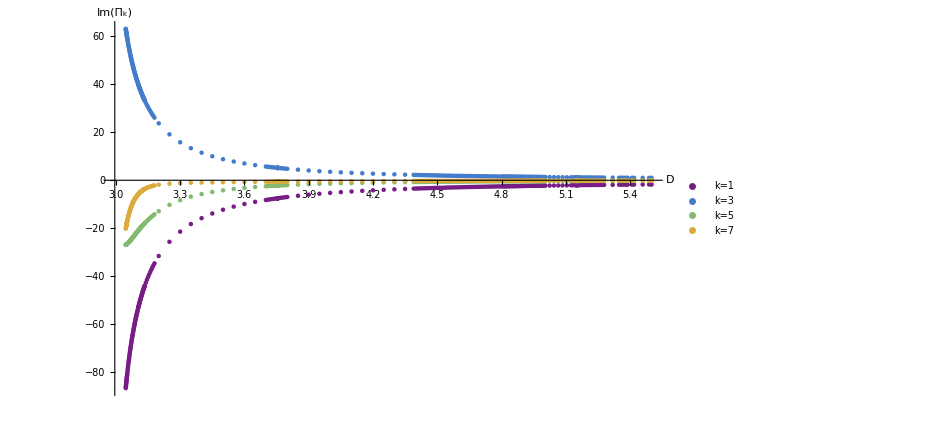

```mathematica
{ListPlot[PicreList,PlotStyle->ColorListmodes,PlotLegends->modelabels,AxesLabel->{"D","Re(Π_k)"},ImageSize->700,BaseStyle->16,PlotRange->All],ListPlot[PicimList,PlotStyle->ColorListmodes,PlotLegends->modelabels,AxesLabel->{"D","Im(Π_k)"},ImageSize->700,BaseStyle->16,PlotRange->All]}
```

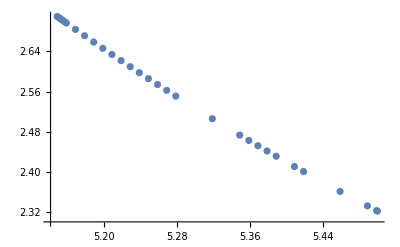

```mathematica
ListPlot[PicreList[[1,;;30,;;]]]
```

```mathematica
ratfit[x_]=(1/(x-3)^c+b)/.FindFit[PicreList[[1,;;100,;;]],1/x^c+b,{b,c},x]
```

2.60823+1/(-3+x)^0.621025

```mathematica
expfit[x_]=Exp[a/(x)]+b/.FindFit[PicreList[[1,;;30,;;]],Exp[a/(x)]+b,{a,b},x]
```

-1.63394+ⅇ^(7.55954/x)

```mathematica
log2fit[x_]=a/Log[(x-2)]+b/.FindFit[PicreList[[1,;;30,;;]],a/Log[(x-2)]+b,{a,b},x]
```

-1.88726+5.27171/Log[-2+x]

```mathematica
logfit[x_]=a/Log[(x)]^2+b/.FindFit[PicreList[[1,;;30,;;]],a/Log[(x)]^2+b,{a,b},x]
```

-2.41697+13.7597/Log[x]^2

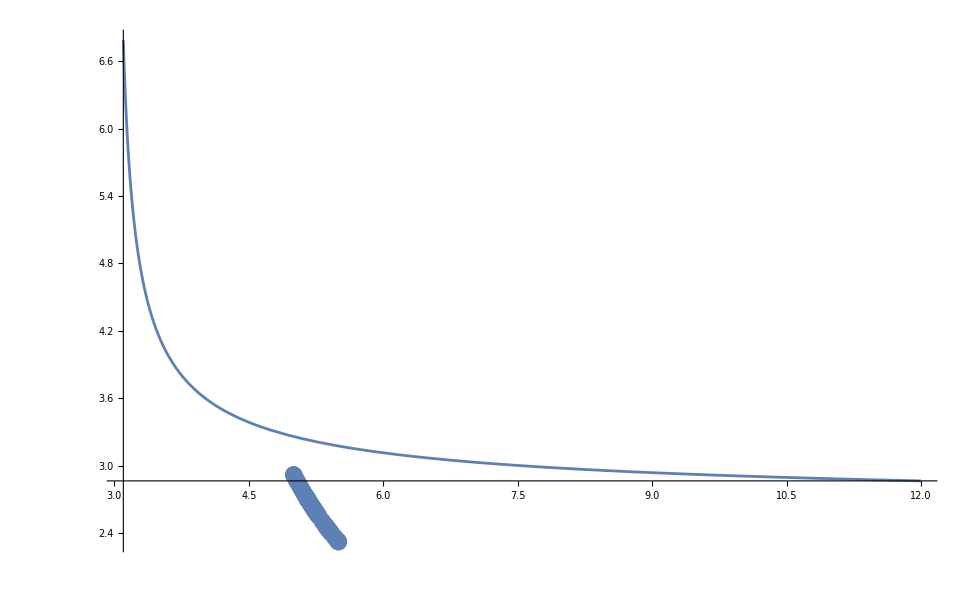

```mathematica
Show[{Plot[ratfit[x],{x,3.1,12},PlotRange->All],ListPlot[PicreList[[1,;;40,;;]]]}]
```

```mathematica
Picspec=1/(√Length[PicList[[1,;;,2]]])Fourier[PicList[[1,;;,2]]];
```

```mathematica
delt=1/(2π)ArcTan[Im[Picspec[[2]]]/Re[Picspec[[2]]]]
```

-0.102478

```mathematica
(*Take just first three modes*)
picApprox[t_]:=Sum[2*Re[Picspec[[2*k]]]Cos[2π*(t)*(2*k-1)]+2*Im[Picspec[[2*k]]]Sin[2π*(t)*(2*k-1)],{k,1,2}];
```

```mathematica
picApprox[t]
```

4.64463 Cos[2 π t]-0.0520563 Cos[6 π t]-3.48627 Sin[2 π t]+1.93546 Sin[6 π t]

```mathematica
picApproxshifted[t_]:=Sum[2*(Re[Picspec[[2*k]]]*Cos[2π(2*k-1)*delt]+Im[Picspec[[2*k]]]*Sin[2π(2*k-1)*delt])Cos[2π*t*(2*k-1)]+2*(Im[Picspec[[2*k]]]*Cos[2π(2*k-1)*delt]-Re[Picspec[[2*k]]]*Sin[2π(2*k-1)*delt])Sin[2π*t*(2*k-1)],{k,1,2}];
```

```mathematica
picApproxshifted[t]
```

0.+5.80747 Cos[2 π t]-1.79242 Cos[6 π t]-0.732085 Sin[6 π t]

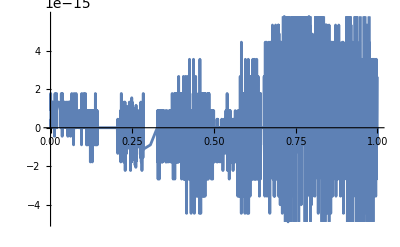

```mathematica
Plot[{picApprox[t+delt]-picApproxshifted[t]},{t,0,1}]
```

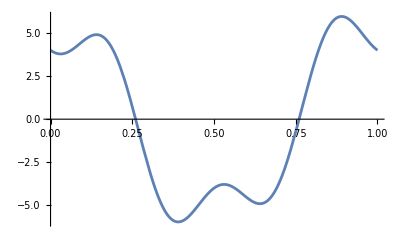

```mathematica
Plot[picApproxshifted[t],{t,0,1}]
```

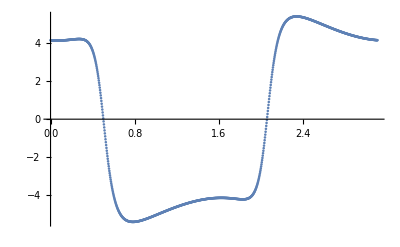

```mathematica
ListPlot[PicList[[1]]]
```

### Check large D Delta condition

```mathematica
testgrid=Range[0,1,1/500];
```

```mathematica
t0List={};
dbeta0List={};
ddbeta0List={};
dddbeta0List={};
ddddbeta0List={};
```

```mathematica
Do[
dPicList=Thread[{PicList[[i,;;,1]],Re[fourdiff[PicList[[i,;;,2]],DeltaList[[i,2]],Length[PicList[[i]]]]]}];
ddPicList=Thread[{dPicList[[;;,1]],Re[fourdiff[dPicList[[;;,2]],DeltaList[[i,2]],Length[dPicList]]]}];
dddPicList=Thread[{ddPicList[[;;,1]],Re[fourdiff[ddPicList[[;;,2]],DeltaList[[i,2]],Length[ddPicList]]]}];
ddddPicList=Thread[{dddPicList[[;;,1]],Re[fourdiff[dddPicList[[;;,2]],DeltaList[[i,2]],Length[dddPicList]]]}];
Picint=Interpolation[PicList[[i]]];
dPicint=Interpolation[dPicList];
ddPicint=Interpolation[ddPicList];
dddPicint=Interpolation[dddPicList];
ddddPicint=Interpolation[ddddPicList];
(*Find root of beta*)
s=Sign[Picint[testgrid[[1]]]];
Do[snow=Sign[Picint[testgrid[[m]]]];
If[s*snow==-1,t0guess=testgrid[[m]];Break[]],{m,2,Length[testgrid]}];
t0now=t/.FindRoot[Picint[t],{t,t0guess}];
AppendTo[t0List,{DeltaList[[i,1]],t0now}];
AppendTo[dbeta0List,{DeltaList[[i,1]],dPicint[t0now]}];
AppendTo[ddbeta0List,{DeltaList[[i,1]],ddPicint[t0now]}];
AppendTo[dddbeta0List,{DeltaList[[i,1]],dddPicint[t0now]}];
AppendTo[ddddbeta0List,{DeltaList[[i,1]],ddddPicint[t0now]}];
,{i,1,Length[dimList]}]
```

#### NLO

```mathematica
NLOList=Thread[{DeltaList[[;;,1]],(Abs@ddbeta0List[[;;,2]])/(3*Abs@dbeta0List[[;;,2]])}];
```

```mathematica
resList=Thread[{DeltaList[[;;,1]],DeltaList[[;;,2]]-(Abs@ddbeta0List[[;;,2]])/(3*Abs@dbeta0List[[;;,2]])}];
```

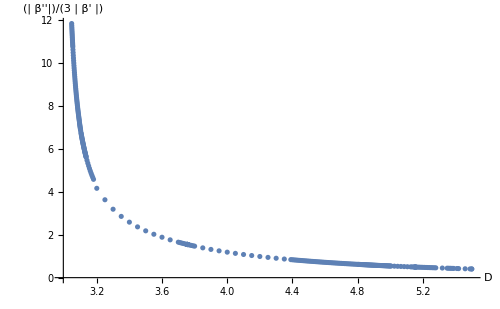

```mathematica
ListPlot[NLOList,BaseStyle->16,AxesLabel->{"D","(| β''|)/(3 | β' |)"},ImageSize->500]
```

#### NNLO

```mathematica
NLOList=Thread[{DeltaList[[;;,1]],Abs@ddbeta0List[[;;,2]]+Abs@dbeta0List[[;;,2]]*(3-4/(DeltaList[[;;,1]]-1))}];
```

```mathematica
NNLOList=Thread[{DeltaList[[;;,1]],Abs@ddddbeta0List[[;;,2]]-55Abs@dbeta0List[[;;,2]]-6(Abs@dbeta0List[[;;,2]])^3+10*Abs@dddbeta0List[[;;,2]]}];
```

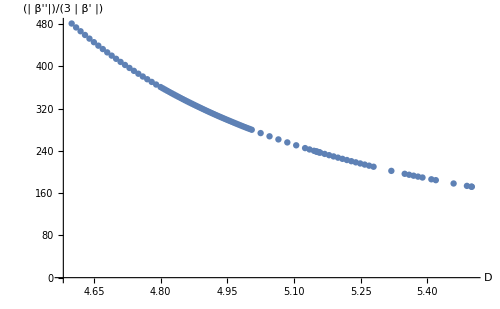
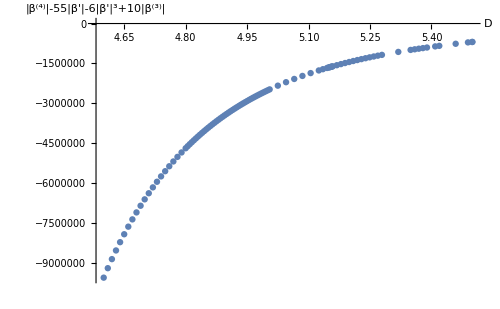

```mathematica
{ListPlot[{NLOList[[;;100]]},BaseStyle->16,AxesLabel->{"D","(| β''|)/(3 | β' |)"},ImageSize->500],ListPlot[{NNLOList[[;;100]]},BaseStyle->16,AxesLabel->{"D","|β^(4)|-55|β'|-6|β'|^3+10|β^(3)|"},ImageSize->500]}
```

#### fmax condition

```mathematica
(1/5.5)^2/(4*DeltaList[[1,2]]^2)*dbeta0List[[1,2]]^2
```

2.2935

### Power spectrum of Ψ_p

```mathematica
nmodes=9;
```

```mathematica
(*modes to take*)
modes=Table[j,{j,1,nmodes,2}]
```

{1,3,5,7,9}

```mathematica
modelabels=Table["k="<>ToString[j-1],{j,2,nmodes,2}]
```

{k=1,k=3,k=5,k=7}

```mathematica
ColorListmodes=Table[ColorData["Rainbow",j/(Length[modes]-1)],{j,0,Length[modes]-1}];
```

```mathematica
PsipimList=Table[{dimList[[i]],1/(√Length[PsipList[[i]]])Im[Fourier[PsipList[[i,;;,2]]][[j]]]},{j,2,nmodes,2},{i,1,Length[dimList]}];
```

```mathematica
PsipreList=Table[{dimList[[i]],1/(√Length[PsipList[[i]]])Re[Fourier[PsipList[[i,;;,2]]][[j]]]},{j,2,nmodes,2},{i,1,Length[dimList]}];
```

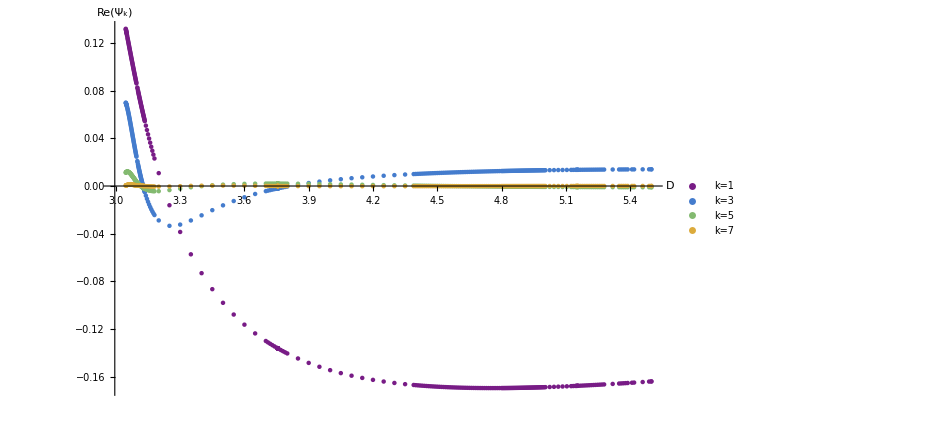
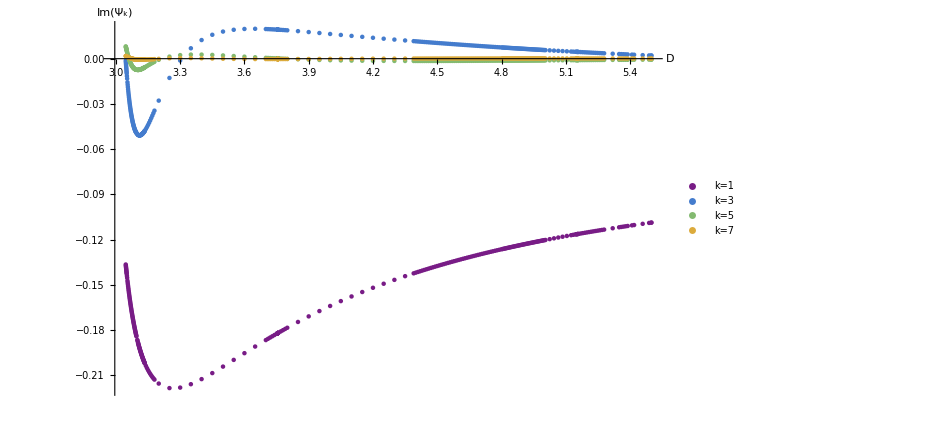

```mathematica
{ListPlot[PsipreList,PlotStyle->ColorListmodes,PlotLegends->modelabels,AxesLabel->{"D","Re(Ψ_k)"},ImageSize->700,BaseStyle->16,PlotRange->All],ListPlot[PsipimList,PlotStyle->ColorListmodes,PlotLegends->modelabels,AxesLabel->{"D","Im(Ψ_k)"},ImageSize->700,BaseStyle->16,PlotRange->All]}
```

### Max (Up)/(4π Δ)

```mathematica
(*Behaviour of max(Up)*)
maxuplist=Table[{DeltaList[[i,1]],Max[UpList[[i,;;,2]]]},{i,1,Length[UpList]}];
```

```mathematica
maxupoverdellist=Table[{DeltaList[[i,1]],Max[UpList[[i,;;,2]]]*4π/DeltaList[[i,2]]},{i,1,Length[UpList]}];
```

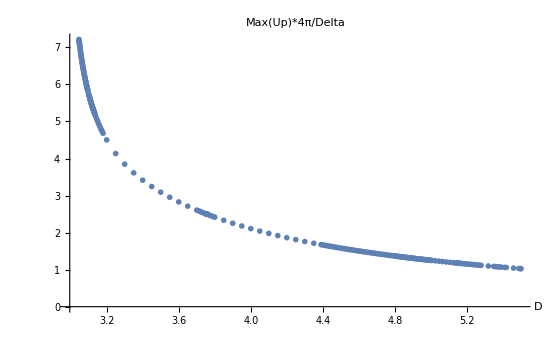

```mathematica
ListPlot[{maxupoverdellist},PlotLabel->"Max(Up)*4π/Delta",AxesLabel->{"D"}]
```

```mathematica
Position[maxupoverdellist[[;;,1]],4.0]
```

{{129}}

```mathematica
uoverdel[dim_]=((dim-3)^a+b)/.FindFit[maxupoverdellist,(dim-3)^a+b,{a,b},dim]
```

0.930061+1/(-3+dim)^0.643277

```mathematica
uoverdel2[dim_]=(a*Log10[(dim-3)/dim]+b)/.FindFit[maxupoverdellist,a*Log10[(dim-3)/dim]+b,{a,b},dim]
```

-0.394089-1.79413 Log[(-3+dim)/dim]

```mathematica
uoverdelover4[dim_]=((dim-3)^a+b)/.FindFit[maxupoverdellist[[;;84]],(dim-3)^a+b,{a,b},dim]
```

0.854332+1/(-3+dim)^1.37529

```mathematica
uoverdel2over4[dim_]=(a*Log10[(dim-3)/dim]+b)/.FindFit[maxupoverdellist[[;;84]],a*Log10[(dim-3)/dim]+b,{a,b},dim]
```

-0.377787-1.77879 Log[(-3+dim)/dim]

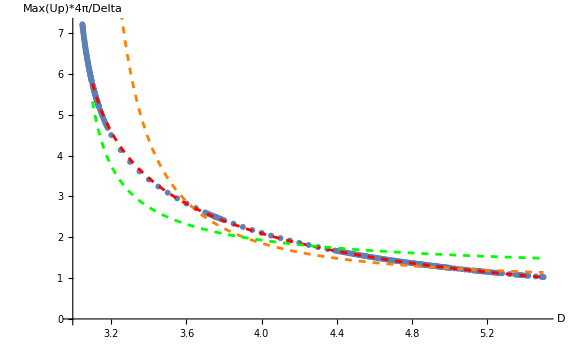

```mathematica
Show[{ListPlot[{maxupoverdellist},AxesLabel->{"D","Max(Up)*4π/Delta"}],Plot[uoverdelover4[dim],{dim,3.1,5.5},PlotStyle->{Dashed,Orange},PlotRange->All],Plot[uoverdel2[dim],{dim,3.1,5.5},PlotStyle->{Dashed,Red},PlotRange->All],Plot[uoverdel[dim],{dim,3.1,5.5},PlotStyle->{Dashed,Green},PlotRange->All]}]
```

### Opening distance of NEC lines

```mathematica
uttestgrid=Range[0.4,2,1/100];
vttestgrid=Range[1.5,3,1/100];
```

```mathematica
UpNECList={};
VpNECList={};
```

```mathematica
Do[
dim=DeltaList[[k,1]];
(*Generate grids*)
delta=DeltaList[[k,2]];
(*Produce interpolations for observables*)
Uint=Interpolation[UpList[[k]]];
Vint=Interpolation[VpList[[k]]];
(*Extract observables*)
(*For the small x-values Findroot needs a really good initial guess; computed here*)
su=Sign[Uint[uttestgrid[[1]]]];
Do[sunow=Sign[Uint[uttestgrid[[m]]]];
If[su*sunow==-1,tu0guess=uttestgrid[[m]];Break[]],{m,2,Length[uttestgrid]}];
uNECsol=FindRoot[Uint[t],{t,tu0guess}];
tu0guess=t/.uNECsol;
(*repeat for V*)
sv=Sign[Vint[vttestgrid[[1]]]];
Do[svnow=Sign[Vint[vttestgrid[[m]]]];
If[sv*svnow==-1,tv0guess=vttestgrid[[m-1]];Break[]],{m,2,Length[vttestgrid]}];
vNECsol=Check[FindRoot[Vint[t],{t,tv0guess}],Continue[]];
tv0guess=t/.vNECsol;
(*Save*)
AppendTo[UpNECList,{dim,tu0guess}];
AppendTo[VpNECList,{dim,tv0guess-delta/2}];
,{k,1,Length[dimList]}]
```

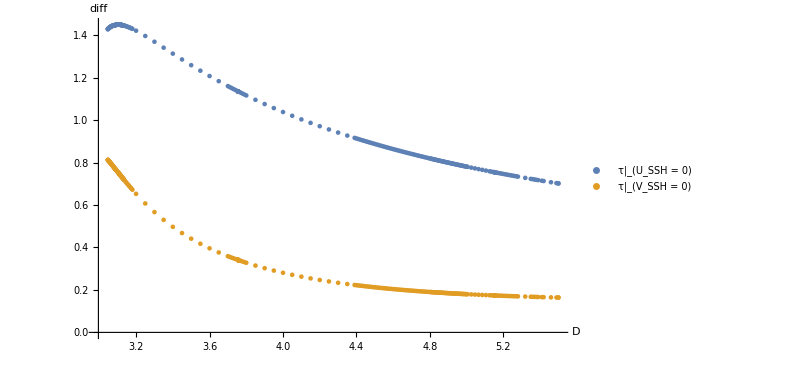

```mathematica
ListPlot[{UpNECList,VpNECList},AxesLabel->{"D","diff"},BaseStyle->16,PlotLegends->{"τ|_(U_SSH = 0)","τ|_(V_SSH = 0)"},ImageSize->600]
```

```mathematica
diffList=Table[{dimList[[i]],UpNECList[[i,2]]-VpNECList[[i,2]]},{i,1,Length[dimList]}];
diffListoverdelta=Table[{dimList[[i]],(UpNECList[[i,2]]-VpNECList[[i,2]])/DeltaList[[i,2]]},{i,1,Length[dimList]}];
```

```mathematica
diffint=Interpolation[diffList];
diffintoverdelta=Interpolation[diffListoverdelta];
```

```mathematica
dvals=Range[3.05,5.5,(5.5-3.05)/500];
```

```mathematica
NECSSHdiff=Thread[{dvals,diffint[dvals]}];
NECSSHdiffoverdelta=Thread[{dvals,diffintoverdelta[dvals]}];
```

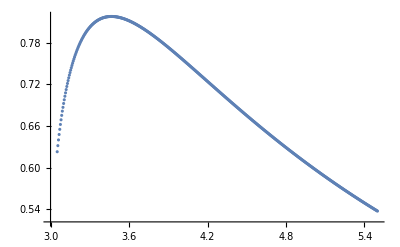
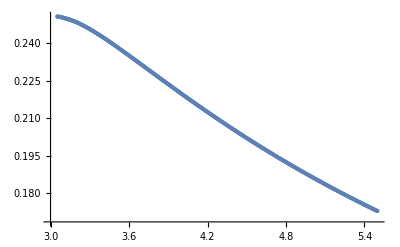

```mathematica
{ListPlot[NECSSHdiff],ListPlot[NECSSHdiffoverdelta]}
```

```mathematica
Export["NECdiffSSH.json",{"NECdiff"->NECSSHdiff}];
Export["NECdiffSSHoverDel.json",{"NECdiff"->NECSSHdiffoverdelta}];
```

## Misc attempts and fits

### Extract data for NEC angle plot

```mathematica
NECvertexList={};
```

```mathematica
tauNEC=0.5;
```

```mathematica
(*Compute NEC vertices*)
Do[
dimnow=DeltaList[[i,1]];
tauNEC=t/.FindRoot[Interpolation[PicList[[i]]][t],{t,tauNEC}];
AppendTo[NECvertexList,{dimnow,tauNEC}]
,{i,1,Length[PicList]}]
```

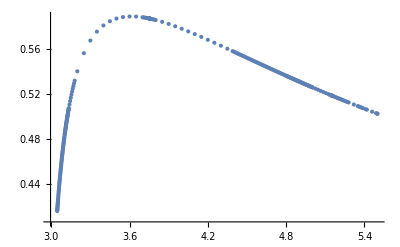

```mathematica
ListPlot[NECvertexList]
```

```mathematica
fNECList={};
```

```mathematica
Do[
dimnow=DeltaList[[i,1]];
fNEC=Interpolation[fcList[[i]]][NECvertexList[[i,2]]];
AppendTo[fNECList,{dimnow,fNEC}]
,{i,1,Length[fcList]}]
```

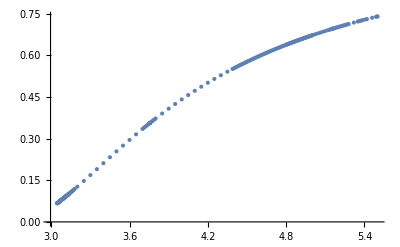

```mathematica
ListPlot[fNECList]
```

```mathematica
Save["NECvertexList.res",NECvertexList];
Save["fNECList.res",fNECList];
```

### Derivatives of Delta

```mathematica
DeltaListdiff=Table[{DeltaList[[i,1]],(DeltaList[[i+1,2]]-DeltaList[[i,2]])/(DeltaList[[i+1,1]]-DeltaList[[i,1]])},{i,1,Length[DeltaList]-1}];
```

```mathematica
DeltaListdiff2=Table[{DeltaList[[i,1]],(DeltaListdiff[[i+1,2]]-DeltaListdiff[[i,2]])/(DeltaListdiff[[i+1,1]]-DeltaListdiff[[i,1]])},{i,1,Length[DeltaList]-2}];
```

```mathematica
DeltaListdiff3=Table[{DeltaList[[i,1]],(DeltaListdiff2[[i+1,2]]-DeltaListdiff2[[i,2]])/(DeltaListdiff2[[i+1,1]]-DeltaListdiff2[[i,1]])},{i,1,Length[DeltaList]-3}];
```

```mathematica
epslistdiff=Table[{DeltaListdiff[[i,1]]-3,DeltaListdiff[[i,2]]},{i,1,Length[DeltaListdiff2]}];
```

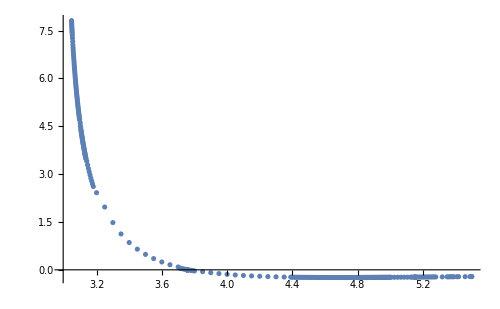
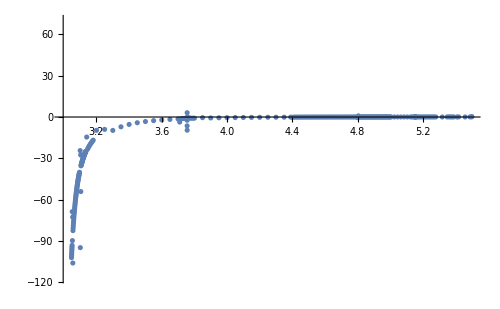
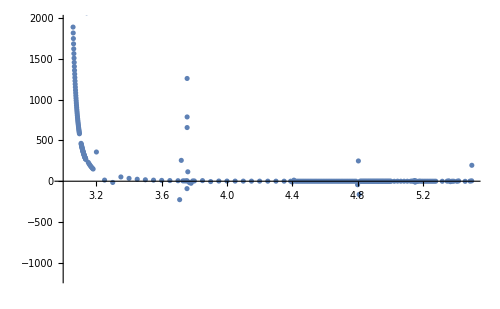

```mathematica
{ListPlot[DeltaListdiff,ImageSize->500],ListPlot[DeltaListdiff2,ImageSize->500],ListPlot[DeltaListdiff3,ImageSize->500]}
```

#### Check for roots

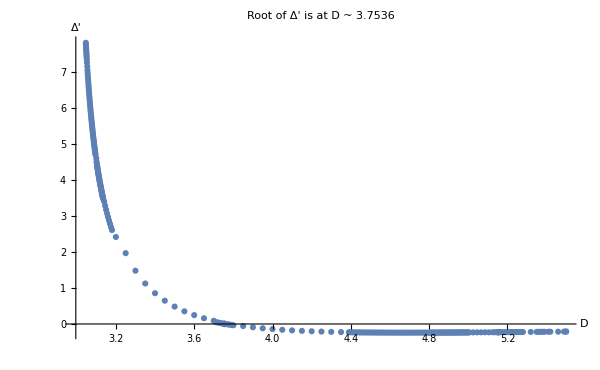

```mathematica
ListPlot[DeltaListdiff,AxesLabel->{"D","Δ'"},BaseStyle->16,ImageSize->600,PlotLabel->"Root of Δ' is at D ~ 3.7536"]
```

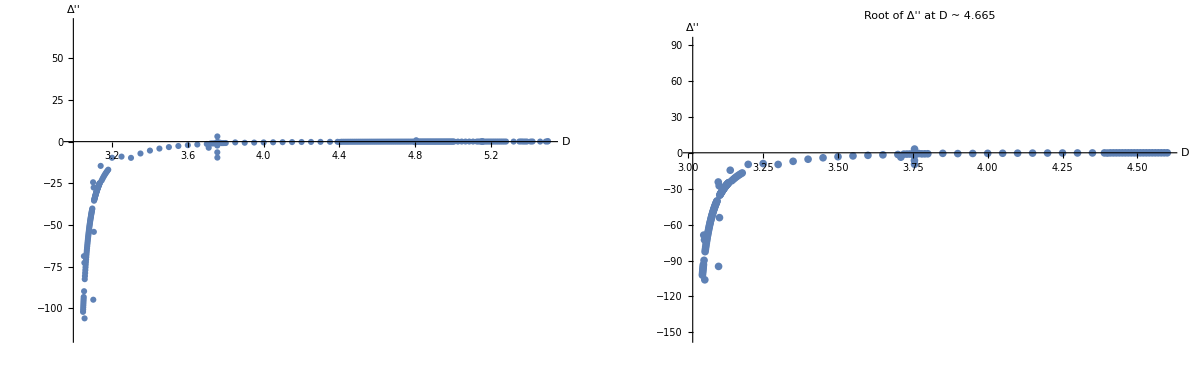

```mathematica
GraphicsRow[{ListPlot[DeltaListdiff2,BaseStyle->16,ImageSize->600,AxesLabel->{"D","Δ''"}],ListPlot[DeltaListdiff2[[100;;]],BaseStyle->16,ImageSize->600,AxesLabel->{"D","Δ''"},PlotLabel->"Root of Δ'' at D ~ 4.665"]},ImageSize->1200]
```

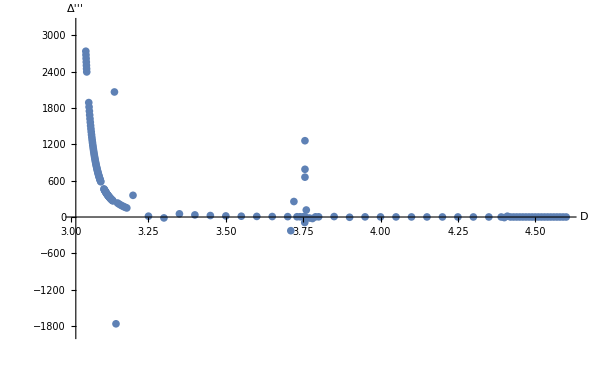

```mathematica
ListPlot[DeltaListdiff3[[100;;]],BaseStyle->16,ImageSize->600,AxesLabel->{"D","Δ'''"}]
```

### Determine small D - 3 behaviour

```mathematica
sortedDelta=Sort[DeltaList];
```

```mathematica
deltalistloglog=Table[{Log10[sortedDelta[[i,1]]-3],Log10[sortedDelta[[i,2]]]},{i,1,Length[DeltaList]}];
```

```mathematica
epslist=Table[{sortedDelta[[i,1]]-3,sortedDelta[[i,2]]},{i,1,Length[DeltaList]}];
```

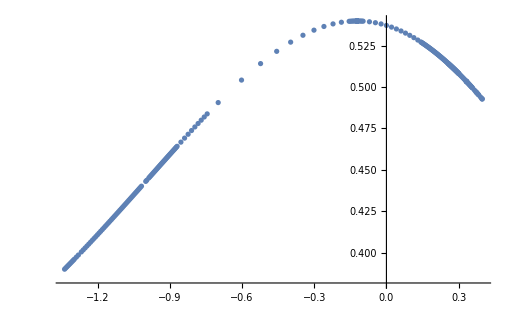

```mathematica
ListPlot[deltalistloglog]
```

```mathematica
deltalog[logeps_]=(a*logeps+b)/.FindFit[deltalistloglog[[;;50]],a*logeps+b,{a,b},logeps]
```

0.599134+0.156731 logeps

```mathematica
10^%//Simplify
```

3.97314 ⅇ^(0.360887 logeps)

```mathematica
a/.FindFit[deltalistloglog[[;;20]],a*logeps+b,{a,b},logeps]
a/.FindFit[deltalistloglog[[21;;55]],a*logeps+b,{a,b},logeps]
a/.FindFit[deltalistloglog[[56;;89]],a*logeps+b,{a,b},logeps]
```

0.151576

0.160748

0.162634

```mathematica
10^0.1599366470788976
```

1.44523

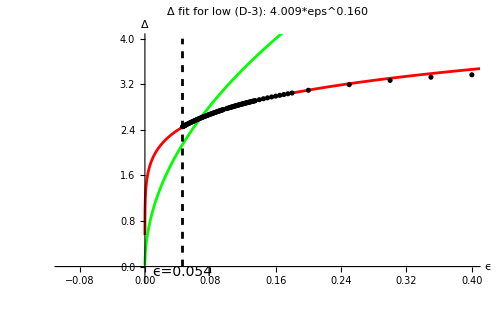

```mathematica
delplot=Show[Plot[4.007*eps^0.160043,{eps,-0.1,0.5},PlotStyle->Red,BaseStyle->16,ImageSize->500,PlotLabel->"Δ fit for low (D-3): 4.009*eps^0.160",AxesLabel->{"ϵ","Δ"},PlotRange->{{-0.1,0.4},{-0.2,4}},Epilog->{Text[Style["ϵ=0.054",14,Black],{0.046,-0.1}]}],Plot[10*eps^0.5,{eps,-0.1,0.5},PlotStyle->Green,BaseStyle->16,ImageSize->500],ListPlot[epslist,PlotStyle->Black],ListPlot[{{0.046,0},{0.046,4}},Joined->True,PlotStyle->{Black,Dashed}]]
```

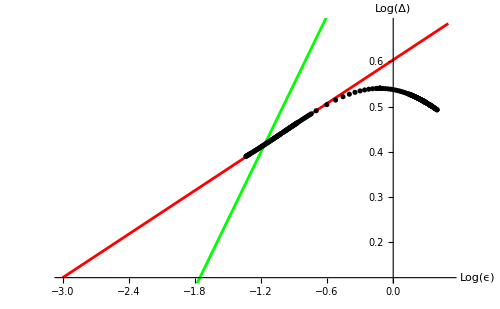

```mathematica
dellogplot=Show[Plot[0.603+0.1601993 logeps,{logeps,-3,0.5},PlotStyle->Red,BaseStyle->16,ImageSize->500,AxesLabel->{"Log(ϵ)","Log(Δ)"}],Plot[1+0.5logeps,{logeps,-3,0.5},PlotStyle->Green,BaseStyle->16,ImageSize->500],ListPlot[deltalistloglog,PlotStyle->Black]]
```

### Instanton - like Delta?

```mathematica
loglog=Table[{Log10[epslist[[i,1]]],Log10[epslist[[i,2]]]},{i,1,Length[epslist]}];
```

```mathematica
dlog=Table[{epslist[[i,1]],(Log10[epslist[[i,2]]]-Log10[epslist[[i-1,2]]])/(epslist[[i,1]]-epslist[[i-1,1]])},{i,2,Length[epslist]}];
```

```mathematica
FindFit[dlog[[;;50]],a/x^(b+1),{a,b},x]
```

{a→0.105465,b→-0.15869}

```mathematica
dlogint=Interpolation[dlog]
```

InterpolatingFunction[…]

```mathematica
xdlog=Table[{epslist[[i,1]],epslist[[i,1]]^0*(Log10[epslist[[i,2]]]-Log10[epslist[[i-1,2]]])/(epslist[[i,1]]-epslist[[i-1,1]])},{i,2,Length[epslist]}];
```

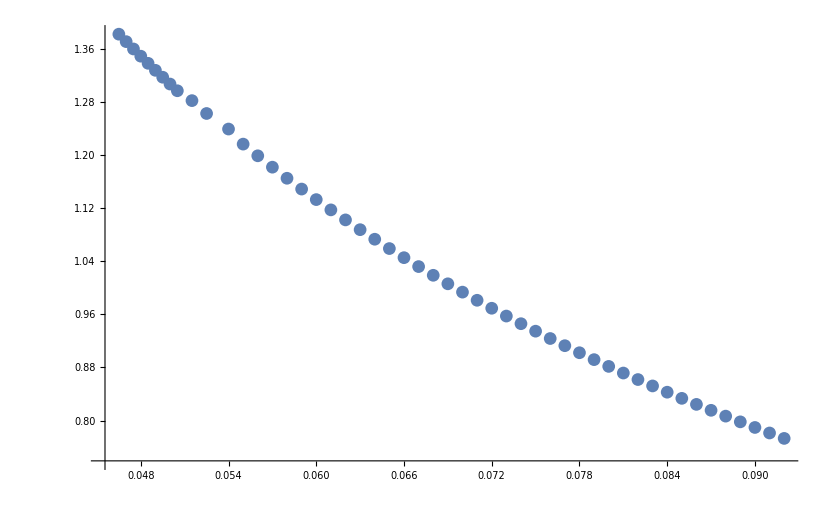

```mathematica
ListPlot[xdlog[[;;50]]]
```

```mathematica
Manipulate[Plot[x^a*dlogint[x],{x,0.055,1}],{a,-1,1.5}]
```

```mathematica
Manipulate[Plot[x^a ⅇ^(-2/x^-0.2),{x,0,5}],{a,0.1,2.5}]
```

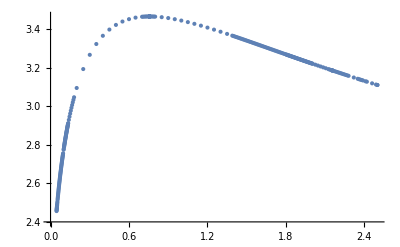

```mathematica
ListPlot[epslist]
```

```mathematica
epslist[[100]]
```

{0.2,3.09474}

```mathematica
Clear[fun]
```

```mathematica
fun[x_]=a*x^b ⅇ^(-x^(3/2)/5)/.FindFit[epslist[[;;100]],a*x^b ⅇ^(-x^(3/2)/5),{a,b},x]
```

4.12348 ⅇ^(-x^(3/2)/5) x^0.169051

```mathematica
RootMeanSquare[Abs[fun[epslist[[;;100,1]]]-epslist[[;;100,2]]]]
```

0.00368315

```mathematica
logfun[x_]=-a/Log10[x]/.FindFit[epslist[[;;100]],-a/Log10[x],{a},x]
```

-6.33116/Log[x]

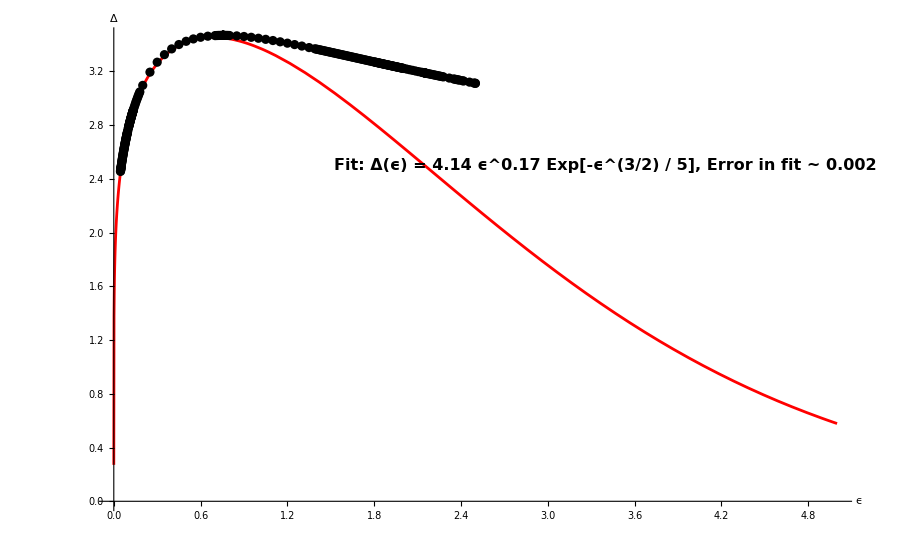

```mathematica
Show[Plot[{fun[x]},{x,0,5},PlotStyle->Red,AxesLabel->{"ϵ","Δ"},BaseStyle->16,Epilog->{Text[Style["Fit: Δ(ϵ) = 4.14 ϵ^0.17 Exp[-ϵ^(3/2) / 5], Error in fit ~ 0.002",16,Bold,Black],{3.4,2.5}]}],ListPlot[epslist,PlotStyle->Black]]
```

### Determine large D behaviour

```mathematica
sortedDeltarev=Reverse[Sort[DeltaList]];
```

```mathematica
deltalistloglogrev=Table[{Log10[1/sortedDeltarev[[i,1]]],Log10[sortedDeltarev[[i,2]]]},{i,1,Length[DeltaList]}];
```

```mathematica
epslistrev=Table[{1/sortedDeltarev[[i,1]],sortedDeltarev[[i,2]]},{i,1,Length[DeltaList]}];
```

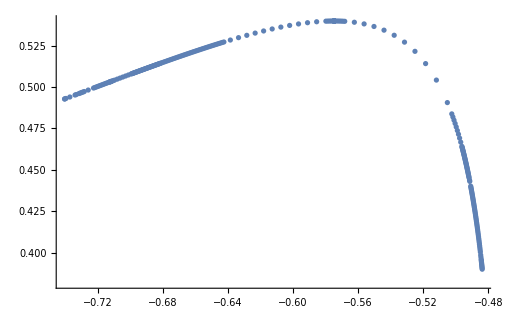

```mathematica
ListPlot[deltalistloglogrev]
```

```mathematica
deltalogrev[logeps_]=(a*logeps+b)/.FindFit[deltalistloglogrev[[;;20]],a*logeps+b,{a,b},logeps]
```

0.768118+0.371882 logeps

```mathematica
10^%//Simplify
```

5.86298 ⅇ^(0.85629 logeps)

```mathematica
a/.FindFit[deltalistloglogrev[[;;20]],a*logeps+b,{a,b},logeps]
a/.FindFit[deltalistloglogrev[[21;;55]],a*logeps+b,{a,b},logeps]
a/.FindFit[deltalistloglogrev[[56;;89]],a*logeps+b,{a,b},logeps]
```

0.371882

0.365449

0.353122

```mathematica
10^0.1599366470788976
```

1.44523

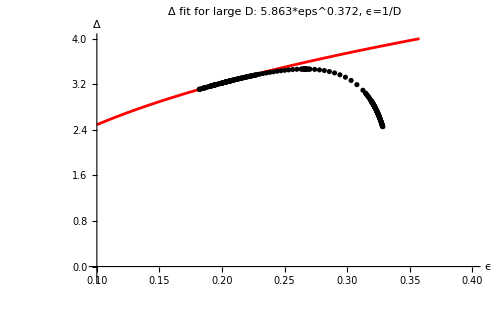

```mathematica
delplot=Show[Plot[5.86297*eps^0.37188,{eps,0.1,0.5},PlotStyle->Red,BaseStyle->16,ImageSize->500,PlotLabel->"Δ fit for large D: 5.863*eps^0.372, ϵ=1/D",AxesLabel->{"ϵ","Δ"},PlotRange->{{0.1,0.4},{-0.2,4}},Epilog->{Text[Style["ϵ=0.054",14,Black],{0.05,-0.1}]}],ListPlot[epslistrev,PlotStyle->Black],ListPlot[{{0.054,0},{0.054,4}},Joined->True,PlotStyle->{Black,Dashed}]]
```

### Planck Law?

```mathematica
planck[x_]=x^b/(ⅇ^(x/T)-1)/.FindFit[epslist,x^b/(ⅇ^(x/T)-1),{T,b},x]
```

x^1.13784/(-1+ⅇ^(0.258425 x))

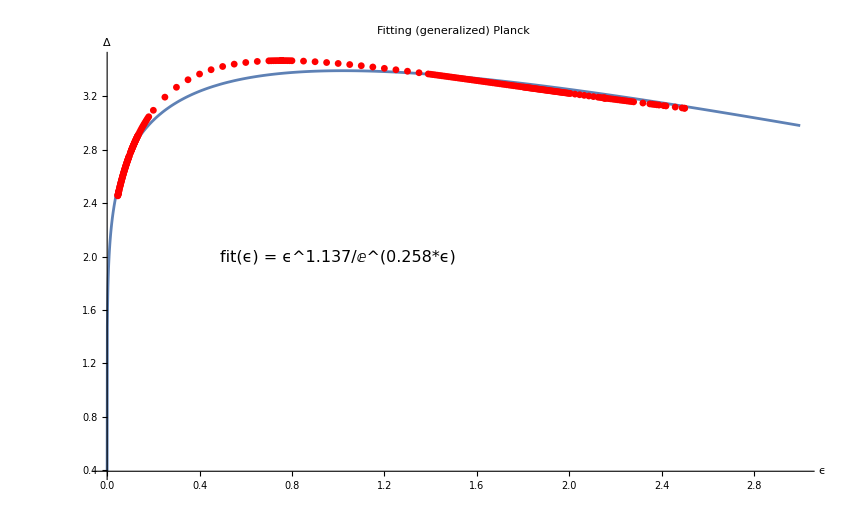

```mathematica
Show[Plot[planck[x],{x,0,3},PlotRange->All,Epilog->{Text[Style["fit(ϵ) = ϵ^1.137/ⅇ^(0.258*ϵ)",16,Black],{1,2}]},AxesLabel->{"ϵ","Δ"},BaseStyle->16,PlotLabel->"Fitting (generalized) Planck"],ListPlot[epslist,PlotStyle->{Red},PlotMarkers->{Automatic, Small}]]
```

### Determine δ of Singular solution at SSH

```mathematica
(*Singular solution parameters*)
(*Extract the zero mode of Up^2 as a function of the dimension*)
upzerosqutab=Sort[Table[{DeltaList[[i,1]],Re[First[1/(√Length[UpList[[i,;;,2]]])Fourier[UpList[[i,;;,2]]*UpList[[i,;;,2]]]]]},{i,1,Length[DeltaList]}]];
```

```mathematica
delta=Table[{upzerosqutab[[i,1]],(2*(upzerosqutab[[i,1]]-2)^3 upzerosqutab[[i,2]]+4*upzerosqutab[[i,1]]-16)/(8-2(upzerosqutab[[i,1]]-2)^3 upzerosqutab[[i,2]])},{i,1,Length[UpList]}];
```

```mathematica
epsfit[dim_]=(a*dim+b)/.FindFit[delta[[;;80]],a*dim+b,{a,b},dim]
```

-3.73829+1.14841 dim

```mathematica
%/.dim->3
```

-0.29305

```mathematica
epsfit2[dim_]=((dim-3)^a+b)/.FindFit[delta[[;;]],(dim-3)^a+b,{a,b},dim]
```

-0.61521+(-3+dim)^0.795318

```mathematica
%/.dim->3
```

-0.61521

```mathematica
epsfit3[dim_]=(a*Log[(dim)]+b)/.FindFit[delta[[;;80]],a*Log[(dim)]+b,{a,b},dim]
```

-4.18134+3.53823 Log[dim]

```mathematica
%/.dim->3
```

-0.2942

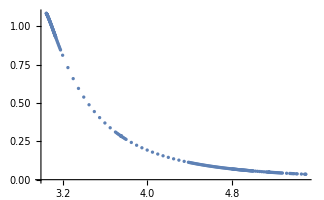

```mathematica
ListPlot[upzerosqutab]
```

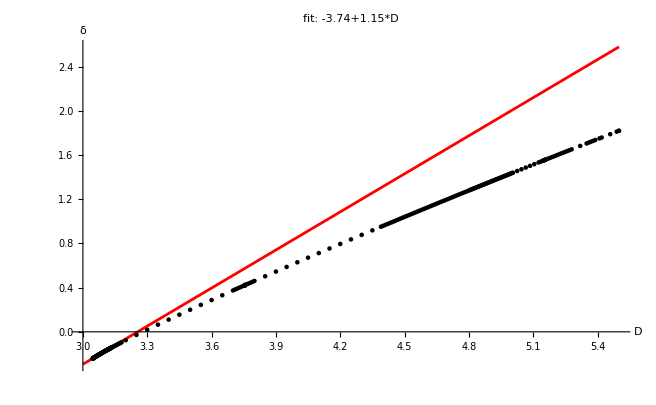

```mathematica
Show[Plot[epsfit[dim],{dim,3,5.5},PlotStyle->Red,BaseStyle->{PointSize[0.01],Thick,14}],ListPlot[delta,BaseStyle->{Black,PointSize[0.005],Thick,8}],PlotLabel->"fit: -3.74+1.15*D",AxesLabel->{"D","δ"}]
```

```mathematica
(*Export["deltaplot.pdf",%]*)
```

```mathematica
(*Try a few different fits*)
```

```mathematica
usqu[dim_]=(a*Log10[(dim-3)/(dim)]+b)/.FindFit[upzerosqutab,a*Log10[(dim-3)/(dim)]+b,{a,b},dim]
```

-0.26883-0.355459 Log[(-3+dim)/dim]

```mathematica
usquexp[dim_]=(a+b*Log10[(dim)/3])/.FindFit[upzerosqutab,a+b*Log10[(dim)/3],{a,b},dim]
```

0.984258-1.93207 Log[dim/3]

```mathematica
usqupoly[dim_]=((dim-3)^a+b)/.FindFit[upzerosqutab,(dim-3)^a+b,{a,b},dim]
```

-0.780098+1/(-3+dim)^0.233238

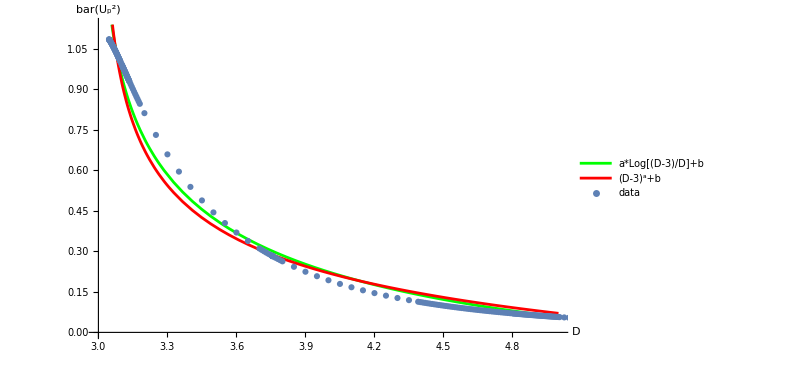

```mathematica
Show[Plot[{usqu[dim],usqupoly[dim]},{dim,3,5},PlotStyle->{Green,Red},AxesLabel->{"D","bar(U_p^2)"},PlotLegends->{"a*Log[(D-3)/D]+b","(D-3)^a+b"}],ListPlot[upzerosqutab,PlotRange->All,PlotLegends->{"data"}],ImageSize->600]
```

#### Check zero mode of e^ω at SSH

```mathematica
psimSSHtab=Table[{DeltaList[[i,1]],√((DeltaList[[i,1]]-2)^3/4)UpList[[i,;;,2]]},{i,1,Length[UpList]}];
```

```mathematica
psimSSHsqutab=Table[{DeltaList[[i,1]],Re[First[1/(√Length[UpList[[i,;;,2]]])Fourier[(DeltaList[[i,1]]-2)^3/4*UpList[[i,;;,2]]*UpList[[i,;;,2]]]]]},{i,1,Length[UpList]}];
```

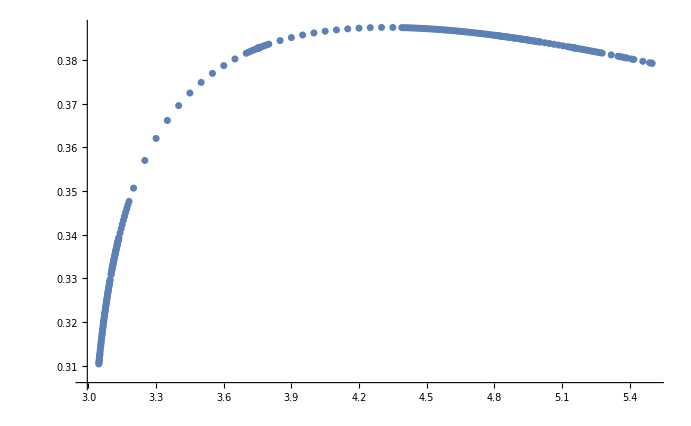

```mathematica
ListPlot[psimSSHsqutab]
```

```mathematica
eomSSHtab=ConstantArray[0,Length[psimSSHtab[[;;,1]]]];
```

```mathematica
Do[ia2list=solinhom[-(psimSSHtab[[i,2]])^2-(psimSSHtab[[i,1]]-3),(psimSSHtab[[i,1]]-3),psimSSHtab[[i,1]],Length[psimSSHtab[[i,2]]]];
eomSSHtab[[i]]={psimSSHtab[[i,1]],1/ia2list};
,{i,1,Length[psimSSHtab[[;;,1]]]}]
```

```mathematica
(*Plot zero mode of e^ω over eps*)
eomSSHzerotab=Table[{DeltaList[[i,1]]-3,Re[First[1/(√Length[eomSSHtab[[i,2]]])Fourier[eomSSHtab[[i,2]]]]]},{i,1,Length[eomSSHtab]}];
```

```mathematica
eomSSHzerotabloglog=Table[{Log10[eomSSHzerotab[[i,1]]],Log10[eomSSHzerotab[[i,2]]]},{i,1,Length[eomSSHzerotab]}];
```

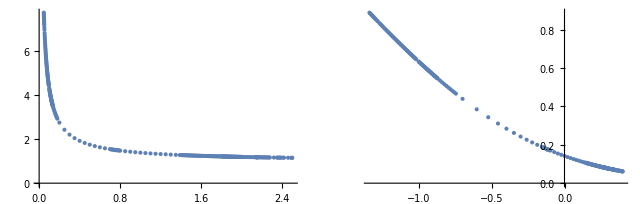

```mathematica
GraphicsRow[{ListPlot[eomSSHzerotab],ListPlot[eomSSHzerotabloglog]}]
```

```mathematica
(*Compute zero mode of ϵe^ω-ϵ (This is the same as the zero mode of psim^2 at the SSH)*)
LHStocheck=Sort[Table[{DeltaList[[i,1]]-3,(DeltaList[[i,1]]-3)*Re[First[1/(√Length[eomSSHtab[[i,2]]])Fourier[eomSSHtab[[i,2]]]]]-(DeltaList[[i,1]]-3)},{i,1,Length[eomSSHtab]}]];
```

```mathematica
LHStochecklog=Table[{Log10[LHStocheck[[i,1]]],Log10[LHStocheck[[i,2]]]},{i,1,Length[LHStocheck]}];
```

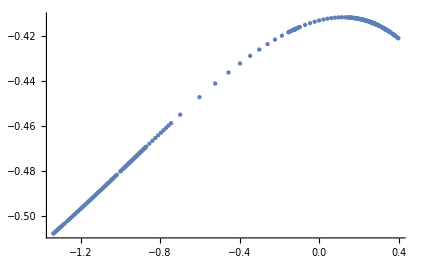

```mathematica
ListPlot[LHStochecklog]
```

```mathematica
LHSfitlog[eps_]=(a*eps+b)/.FindFit[LHStochecklog[[;;40]],a*eps+b,{b,a},eps]
```

-0.399589+0.0811667 eps

```mathematica
10^(%)
```

10^(-0.399589+0.0811667 eps)

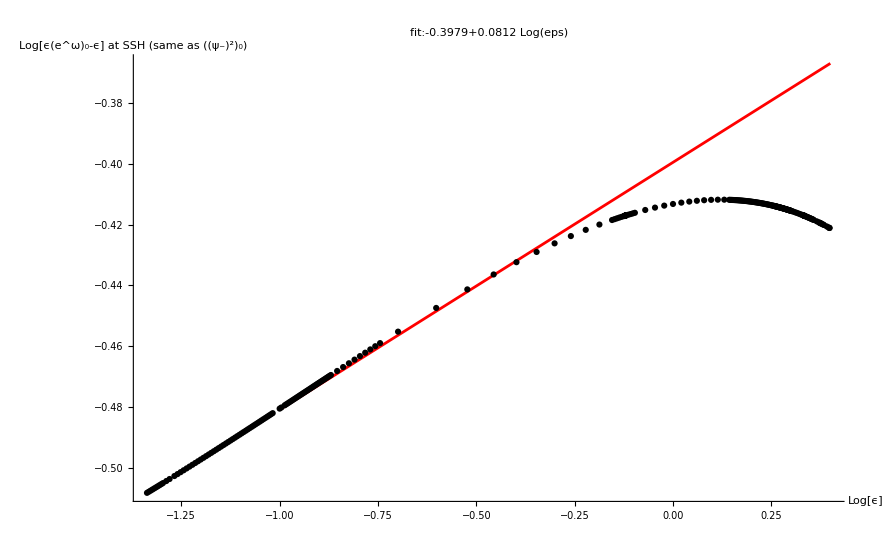

```mathematica
Show[Plot[{LHSfitlog[x]},{x,-1,0.4},PlotRange->All,PlotStyle->Red,PlotLabel->"fit:-0.3979+0.0812 Log(eps) ",AxesLabel->{"Log[ϵ]","Log[ϵ(e^ω)_0-ϵ] at SSH (same as ((ψ_-)^2)_0)"},BaseStyle->16],ListPlot[LHStochecklog,PlotStyle->Black,BaseStyle->{Black,PointSize[0.005],Thick,8}]]
```

```mathematica
(*check full equation*)
eqcheck=Table[{DeltaList[[i,1]]-3,(DeltaList[[i,1]]-3)*Re[First[1/(√Length[eomSSHtab[[i,2]]])Fourier[eomSSHtab[[i,2]]]]]-(DeltaList[[i,1]]-3)-psimSSHsqutab[[i,2]]},{i,1,Length[eomSSHtab]}];
```

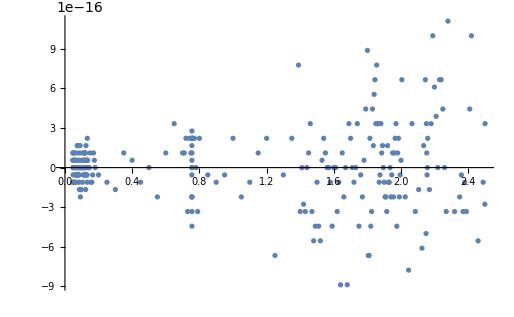

```mathematica
ListPlot[eqcheck]
```

```mathematica
lambdapole=Sort[Table[{DeltaList[[i,1]],(DeltaList[[i,1]]-3)Re[First[1/(√Length[eomSSHtab[[i,2]]])Fourier[eomSSHtab[[i,2]]]]]},{i,1,Length[eomSSHtab]}]];
```

### Locations of pole and zero (breakdown of perturbation computation)

```mathematica
(*This is for the discussion about why the perturbations do not work any more between D=4.8 and 5.2, needs background data over x as input
still needs to be processed if we want to show such a plot. (Here it is just compied from some local notebook I have) *)
```

```mathematica
eomzeromax={{3.2,1.5301491198307255},{3.4,1.4854511943464839},{3.6,1.558386773935549},{3.8,1.6724531440625416},{4.,1.807516245250779},{4.2,1.9554223374704445},{4.4,2.112064279024339},{4.6,2.2750849902613126},{4.8,2.4429999256129804},{5.,2.6147913473849087}};
lambdalower={{3.2,0.20000000000000018},{3.4,0.3999999999999999},{3.6,0.6000000000000001},{3.8,0.7999999999999998},{4.,1.},{4.2,1.2000000000000002},{4.4,1.4000000000000004},{4.6,1.5999999999999996},{4.8,1.7999999999999998},{5.,2.}};
```

```mathematica
lambroot=Table[{GammaList512[[i,1]],1/GammaList512[[i,2]]},{i,1,Length[GammaList512]}];
```

```mathematica
lambrootint=Interpolation[lambroot];
```

```mathematica
lamlow=Interpolation[lambdalower];
lamup=Interpolation[eomzeromax];
```

```mathematica
FindRoot[lambrootint[dim]-lamup[dim],{dim,5}]
```

{dim→4.80754}

```mathematica
lamup[4]
```

1.80752

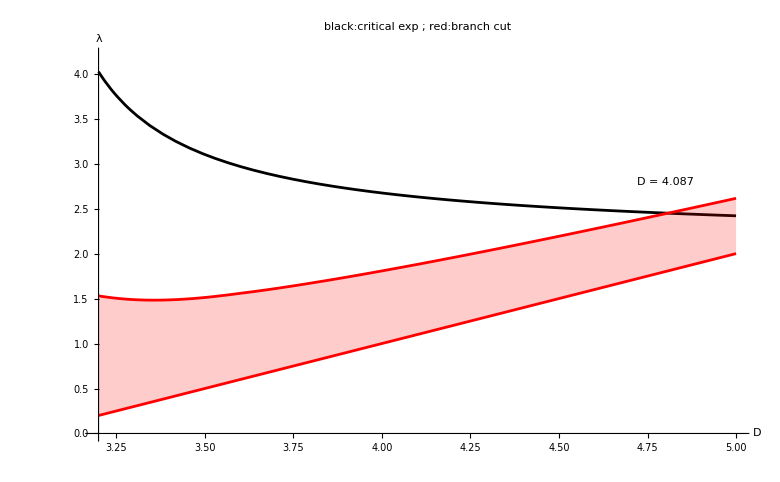

```mathematica
Show[Plot[lambrootint[dim],{dim,3.2,5},PlotStyle->Black,PlotRange->{{3.2,5},{0,4.2}},BaseStyle->16,AxesLabel->{"D","λ"},Epilog->Inset["D = 4.087",{4.8,2.8}],PlotLabel->"black:critical exp ; red:branch cut"],Plot[{lamlow[dim],lamup[dim]},{dim,3.2,5},Filling->{1->{2}},PlotStyle->Red]]
```

## Initial data plots and animations

### Plot Initial data over D

```mathematica
ColorList=Table[ColorData["Rainbow",j/(Length[UpList]-1)],{j,0,Length[UpList]-1}];
```

```mathematica
{ListPlot[UpList,Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","U_p"},BaseStyle->16,ImageSize->500],
ListPlot[psicList,Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","ψ_c"},BaseStyle->16,ImageSize->500],
ListPlot[fcList,Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","f_c"},BaseStyle->16,ImageSize->500]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
fcListnormed={};
fcListnormedmax={};
dtfcListnormed={};
PsicListnormed={};
PsicListnormedmax={};
PicListnormed={};
PicListnormedmax={};
dtPicListnormed={};
ddtPicListnormed={};
dyPicListnormed={};
OmcListnormed={};
OmcListnormedmax={};
PipListnormed={};
PipListnormedmax={};
PsipListnormed={};
PsipListnormedmax={};
```

```mathematica
Do[fcNow=fcList[[i,;;,2]];
dtfcNow=dtfcList[[i,;;,2]];
psicNow=psicList[[i,;;,2]];
PipNow=PipList[[i,;;,2]];
PsipNow=PsipList[[i,;;,2]];
picNow=PicList[[i,;;,2]];
dtpicNow=dtPicList[[i,;;,2]];
ddtpicNow=ddtPicList[[i,;;,2]];
dypicNow=dyPicList[[i,;;,2]];
OmcNow=OmcList[[i,;;,2]];
tauList=fcList[[i,;;,1]];
DeltaNow=DeltaList[[i,2]];
AppendTo[fcListnormed,Thread[{tauList[[;;]]/DeltaNow,fcNow}]];
AppendTo[fcListnormedmax,Thread[{tauList[[;;]]/DeltaNow,fcNow/Max[fcNow]}]];
AppendTo[dtfcListnormed,Thread[{tauList[[;;]]/DeltaNow,dtfcNow}]];
AppendTo[PsicListnormed,Thread[{tauList[[;;]]/DeltaNow,psicNow}]];
AppendTo[PsicListnormedmax,Thread[{tauList[[;;]]/DeltaNow,psicNow/Max[psicNow]}]];
AppendTo[PicListnormed,Thread[{tauList[[;;]]/DeltaNow,picNow}]];
AppendTo[PicListnormedmax,Thread[{tauList[[;;]]/DeltaNow,picNow/Max[picNow]}]];
AppendTo[dtPicListnormed,Thread[{tauList[[;;]]/DeltaNow,dtpicNow}]];
AppendTo[ddtPicListnormed,Thread[{tauList[[;;]]/DeltaNow,ddtpicNow}]];
AppendTo[dyPicListnormed,Thread[{tauList[[;;]]/DeltaNow,dypicNow}]];
AppendTo[OmcListnormed,Thread[{tauList[[;;]]/DeltaNow,OmcNow}]];
AppendTo[OmcListnormedmax,Thread[{tauList[[;;]]/DeltaNow,OmcNow/Max[OmcNow]}]];
AppendTo[PipListnormed,Thread[{tauList[[;;]]/DeltaNow,PipNow}]];
AppendTo[PipListnormedmax,Thread[{tauList[[;;]]/DeltaNow,PipNow/Max[PipNow]}]];
AppendTo[PsipListnormed,Thread[{tauList[[;;]]/DeltaNow,PsipNow}]];
AppendTo[PsipListnormedmax,Thread[{tauList[[;;]]/DeltaNow,PsipNow/Max[PsipNow]}]];
,{i,1,Length[DeltaList]}]
```

```mathematica
{ListPlot[fcListnormed,Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","f_c"},BaseStyle->16,ImageSize->500],
ListPlot[fcListnormedmax,Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","f_c"},BaseStyle->16,ImageSize->500]}
```

{-Graphics-,-Graphics-}

```mathematica
{ListPlot[PsicListnormed,Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","Ψ_c"},BaseStyle->16,ImageSize->500],
ListPlot[PsicListnormedmax,Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","Ψ_c"},BaseStyle->16,ImageSize->500,PlotRange->All]}
```

{-Graphics-,-Graphics-}

```mathematica
{ListPlot[PipListnormed,Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","Π_p"},BaseStyle->16,ImageSize->500],
ListPlot[PipListnormedmax,Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","Π_p"},BaseStyle->16,ImageSize->500]}
```

{-Graphics-,-Graphics-}

```mathematica
{ListPlot[PsipListnormed,Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","Ψ_p"},BaseStyle->16,ImageSize->500],
ListPlot[PsipListnormedmax,Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","Ψ_p"},BaseStyle->16,ImageSize->500]}
```

{-Graphics-,-Graphics-}

```mathematica
{ListPlot[OmcListnormed,Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","Ω_c"},BaseStyle->16,ImageSize->500],
ListPlot[OmcListnormedmax[[1]],Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","Ω_c"},BaseStyle->16,ImageSize->500]}
```

{-Graphics-,-Graphics-}

```mathematica
{ListPlot[PicListnormed,Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","Π_c"},BaseStyle->16,ImageSize->500,PlotRange->All],ListPlot[PicListnormedmax,Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","Π_c"},BaseStyle->16,ImageSize->500,PlotRange->All]}
```

{-Graphics-,-Graphics-}

#### 3D Plots

```mathematica
(*Produce 3D Plots with the Dimension on the third axis*)
```

```mathematica
Omc3DList=Flatten[Table[{dimList[[i]],OmcListnormed[[i,j,1]],OmcListnormed[[i,j,2]]},{i,1,Length[dimList],4},{j,1,Length[OmcListnormed[[i]]],8}],1];
```

```mathematica
Omc3DList//Dimensions
```

{10368,3}

```mathematica
ListPlot3D[Omc3DList,PlotRange->All,ImageSize->800,AxesLabel->{"D","τ","Ω_c"},BaseStyle->{16,Black},LabelStyle->Directive[Black,Bold]]
```

-Graphics3D-

### About the Relation Ω = (D-3)/(D-1)Π^2

```mathematica
PisquaredcListnormed={};
```

```mathematica
Do[picNow=PicList[[i,;;,2]];
tauList=PicList[[i,;;,1]];
DeltaNow=DeltaList[[i,2]];
AppendTo[PisquaredcListnormed,Thread[{tauList[[;;]]/DeltaNow,picNow^2}]];
,{i,1,Length[DeltaList]}]
```

```mathematica
{ListPlot[OmcListnormed,Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","Ω_c"},BaseStyle->16,ImageSize->500,PlotRange->All],
ListPlot[PisquaredcListnormed,Joined->True,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","Π_c^2"},BaseStyle->16,ImageSize->500,PlotRange->All]}
```

{-Graphics-,-Graphics-}

```mathematica
(*None of these functions goes to zero for low D*)
```

```mathematica
ListPlot[OmcListnormed[[-1]],Joined->True,Frame->True,FrameLabel->{"τ","Ω_c"},BaseStyle->16,ImageSize->500,PlotRange->All]
```

-Graphics-

### Plot coefficients of Heat equation

```mathematica
coeff0=Flatten[Table[{dimList[[i]],PicListnormed[[i,j,1]],ddtPicListnormed[[i,j,2]]},{i,1,Length[dimList],4},{j,1,Length[OmcListnormed[[i]]],8}],1];
c0=ListPlot3D[coeff0,PlotRange->All,ImageSize->800,AxesLabel->{"D","τ","(∂_τ)^2Π_c"},BaseStyle->{16,Black},LabelStyle->Directive[Black,Bold]];
```

```mathematica
coeff1=Flatten[Table[{dimList[[i]],PicListnormed[[i,j,1]],3dtPicListnormed[[i,j,2]]},{i,1,Length[dimList],4},{j,1,Length[OmcListnormed[[i]]],8}],1];
```

```mathematica
c1=ListPlot3D[coeff1,PlotRange->All,ImageSize->800,AxesLabel->{"D","τ","3∂_τ Π_c"},BaseStyle->{16,Black},LabelStyle->Directive[Black,Bold]];
```

```mathematica
coeff2=Flatten[Table[{dimList[[i]],PicListnormed[[i,j,1]],2PicListnormed[[i,j,2]]},{i,1,Length[dimList],4},{j,1,Length[PicListnormed[[i]]],8}],1];
```

```mathematica
c2=ListPlot3D[coeff2,PlotRange->All,ImageSize->800,AxesLabel->{"D","τ","2Π_c"},BaseStyle->{16,Black},LabelStyle->Directive[Black,Bold]];
```

```mathematica
coeff3=Flatten[Table[{dimList[[i]],PicListnormed[[i,j,1]],1/fcListnormed[[i,j,2]] dtPicListnormed[[i,j,2]]*dtfcListnormed[[i,j,2]]},{i,1,Length[dimList],4},{j,1,Length[OmcListnormed[[i]]],8}],1];
```

```mathematica
c3=ListPlot3D[coeff3,PlotRange->All,ImageSize->800,AxesLabel->{"D","τ","∂_τ Π_c ∂_τ Log f_c"},BaseStyle->{16,Black},LabelStyle->Directive[Black,Bold]];
```

```mathematica
coeff4=Flatten[Table[{dimList[[i]],PicListnormed[[i,j,1]],1/fcListnormed[[i,j,2]] PicListnormed[[i,j,2]]*dtfcListnormed[[i,j,2]]},{i,1,Length[dimList],4},{j,1,Length[OmcListnormed[[i]]],8}],1];
c4=ListPlot3D[coeff4,PlotRange->All,ImageSize->800,AxesLabel->{"D","τ","Π_c ∂_τ Log f_c"},BaseStyle->{16,Black},LabelStyle->Directive[Black,Bold]];
```

```mathematica
coeff5=Flatten[Table[{dimList[[i]],PicListnormed[[i,j,1]],(dimList[[i]]-3)*fcListnormed[[i,j,2]]^2 PicListnormed[[i,j,2]]^3},{i,1,Length[dimList],4},{j,1,Length[OmcListnormed[[i]]],8}],1];
```

```mathematica
c5=ListPlot3D[coeff5,PlotRange->All,ImageSize->800,AxesLabel->{"D","τ","(D-3)f_c^2Π_c^3"},BaseStyle->{16,Black},LabelStyle->Directive[Black,Bold]];
```

```mathematica
coeff6=Flatten[Table[{dimList[[i]],PicListnormed[[i,j,1]],2(dimList[[i]]-1)*fcListnormed[[i,j,2]]^2 dyPicListnormed[[i,j,2]]},{i,1,Length[dimList],4},{j,1,Length[OmcListnormed[[i]]],8}],1];
```

```mathematica
c6=ListPlot3D[coeff6,PlotRange->All,ImageSize->800,AxesLabel->{"D","τ","2(D-1)f_c^2∂_y Π_c"},BaseStyle->{16,Black},LabelStyle->Directive[Black,Bold]];
```

```mathematica
GraphicsGrid[{{c0,c1,c2,"dummy"},{c3,c4,c5,c6}},ImageSize->1500]
```

-Graphics-

```mathematica
l0=ListPlot[Thread[{PicListnormed[[-1,;;,1]],ddtPicListnormed[[-1,;;,2]]}],Joined->True,PlotRange->All,Frame->True,BaseStyle->16,FrameLabel->{"τ","(∂_τ)^2Π_c"},ImageSize->500];
l1=ListPlot[Thread[{PicListnormed[[-1,;;,1]],3dtPicListnormed[[-1,;;,2]]}],Joined->True,PlotRange->All,Frame->True,BaseStyle->16,FrameLabel->{"τ","3∂_τ Π_c"},ImageSize->500];
l2=ListPlot[Thread[{PicListnormed[[-1,;;,1]],2PicListnormed[[-1,;;,2]]}],Joined->True,PlotRange->All,Frame->True,BaseStyle->16,FrameLabel->{"τ","2Π_c"},ImageSize->500];
l3=ListPlot[Thread[{PicListnormed[[-1,;;,1]],1/fcListnormed[[-1,;;,2]] dtPicListnormed[[-1,;;,2]]*dtfcListnormed[[-1,;;,2]]}],Joined->True,PlotRange->All,Frame->True,BaseStyle->16,FrameLabel->{"τ","∂_τ Π_c ∂_τ Log f_c"},ImageSize->500];
l4=ListPlot[Thread[{PicListnormed[[-1,;;,1]],1/fcListnormed[[-1,;;,2]] PicListnormed[[-1,;;,2]]*dtfcListnormed[[-1,;;,2]]}],Joined->True,PlotRange->All,Frame->True,BaseStyle->16,FrameLabel->{"τ","Π_c ∂_τ Log f_c"},ImageSize->500];
l5=ListPlot[Thread[{PicListnormed[[-1,;;,1]],(dimList[[-1]]-3)*fcListnormed[[-1,;;,2]]^2 PicListnormed[[-1,;;,2]]^3}],Joined->True,PlotRange->All,Frame->True,BaseStyle->16,FrameLabel->{"τ","(D-3)f_c^2Π_c^3"},ImageSize->500];
l6=ListPlot[Thread[{PicListnormed[[-1,;;,1]],2(dimList[[-1]]-1)*fcListnormed[[-1,;;,2]]^2 dyPicListnormed[[-1,;;,2]]}],Joined->True,PlotRange->All,Frame->True,BaseStyle->16,FrameLabel->{"τ","2(D-1)f_c^2∂_y Π_c"},ImageSize->500];
```

```mathematica
GraphicsGrid[{{l0,l1,l2,"dummy"},{l3,l4,l5,l6}},ImageSize->1500]
```

-Graphics-

### Spectra

```mathematica
extractspec[f_,Nt_]:=Module[{},Abs[1/(√Nt)Fourier[dealias[f,Nt]]][[;;Nt/2]]];
```

```mathematica
Upaux=UpList[[;;,;;,2]];
fcaux=fcList[[;;,;;,2]];
psicaux=psicList[[;;,;;,2]];
```

```mathematica
Upspec=extractspec[#,512]&/@Upaux;
fcspec=extractspec[#,512]&/@fcaux;
psicspec=extractspec[#,512]&/@psicaux;
```

```mathematica
ListPlot[Table[{DeltaList[[i,1]]},{i,1,Length[DeltaList[[;;,1]]]}],PlotStyle->ColorList]
```

-Graphics-

```mathematica
{ListLogPlot[Upspec,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","Abs(U_pk)"},BaseStyle->16,ImageSize->500,PlotMarkers->{Automatic, Tiny}],
ListLogPlot[psicspec,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","Abs(ψ_ck)"},BaseStyle->16,ImageSize->500,PlotMarkers->{Automatic, Tiny}],
ListLogPlot[fcspec,PlotStyle->ColorList,Frame->True,FrameLabel->{"τ","Abs(f_ck)"},BaseStyle->16,ImageSize->500,PlotMarkers->{Automatic, Tiny}]}
```

{-Graphics-,-Graphics-,-Graphics-}

### Animations

```mathematica
(*Commended out since this takes quite long to evaluate*)
```

```mathematica
(* animation, not that the 512 mode results have gaps in D *)
(*ListAnimate[Table[ListPlot[UpList[[i]],Joined->True,PlotStyle->ColorList[[i]],Frame->True,FrameLabel->{"τ","U_p"},BaseStyle->16,ImageSize->500,PlotRange->{{0,3.5},{-1.5,1.5}},PlotLabel->"D="<>ToString[DeltaList[[i,1]]]],{i,Length[UpList]}]]*)
```

```mathematica
(* animation, not that the 512 mode results have gaps in D *)
(*ListAnimate[Table[ListPlot[psicList[[i]],Joined->True,PlotStyle->ColorList[[i]],Frame->True,FrameLabel->{"τ","ψ_c"},BaseStyle->16,ImageSize->500,PlotRange->{{0,3.5},{-100,100}},PlotLabel->"D="<>ToString[DeltaList[[i,1]]]],{i,Length[UpList]}]]*)
```

### Initial Data Plot at fixed D

```mathematica
(* dimension and Delta *)
iNow=1;
{DimNow,DeltaNow}=DeltaList[[iNow]];
(* interpolating function *)
UpInt=Interpolation[UpList[[iNow]]];
psicInt=Interpolation[psicList[[iNow]]];
fcInt=Interpolation[fcList[[iNow]]];
{Plot[UpInt[t],{t,0,DeltaNow},Frame->True,FrameLabel->{"τ","U_p"},BaseStyle->16,ImageSize->500,PlotLabel->"D="<>ToString[DimNow]],
Plot[psicInt[t],{t,0,DeltaNow},Frame->True,FrameLabel->{"τ","ψ_c"},BaseStyle->16,ImageSize->500,PlotLabel->"D="<>ToString[DimNow],PlotRange->All],
Plot[fcInt[t],{t,0,DeltaNow},Frame->True,FrameLabel->{"τ","f_c"},BaseStyle->16,ImageSize->500,PlotLabel->"D="<>ToString[DimNow],PlotRange->All]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Daniel's guess for fc at lowest D*)
Plot[{0.025*Sum[Cos[2 n x]/2^n,{n,0,64}],fcInt[x*DeltaNow/(2π)]},{x,0,2 Pi},PlotLegends->{"guess","fc"},PlotLabel->"fc at D = 3.046",BaseStyle->16,ImageSize->500]
```

-Graphics-

```mathematica
{ListPlot[PipList[[1]],PlotRange->All],ListPlot[PsipList[[1]],PlotRange->All]}
```

{-Graphics-,-Graphics-}

### Extract Π_c for D->Infinity model

```mathematica
dim=DeltaList[[1,1]]
```

5.5

```mathematica
delta=DeltaList[[1,2]]
```

3.1102

```mathematica
pic=Thread[{PicList[[1,;;,1]]/delta,PicList[[1,;;,2]]}];
```

```mathematica
dpic=Thread[{PicList[[1,;;,1]]/delta,Re[fourdiff[PicList[[1,;;,2]],delta,Length[PicList[[1,;;,2]]]]]}];
```

```mathematica
ddpic=Thread[{PicList[[1,;;,1]]/delta,Re[fourdiff[dpic[[;;,2]],delta,Length[PicList[[1,;;,2]]]]]}];
```

```mathematica
dddpic=Thread[{PicList[[1,;;,1]]/delta,Re[fourdiff[ddpic[[;;,2]],delta,Length[PicList[[1,;;,2]]]]]}];
```

```mathematica
ddddpic=Thread[{PicList[[1,;;,1]]/delta,Re[fourdiff[dddpic[[;;,2]],delta,Length[PicList[[1,;;,2]]]]]}];
```

```mathematica
(*Export["pic.dat",pic];*)
```

```mathematica
(*Export["dpic.dat",dpic];*)
```

```mathematica
(*Export["ddpic.dat",ddpic];*)
```

```mathematica
(*Export["dddpic.dat",dddpic];*)
```

```mathematica
(*Export["ddddpic.dat",ddddpic];*)
```

```mathematica
(*Export["Delta.dat",delta];*)
```

```mathematica
ListPlot[dddpic,Joined->True]
```

-Graphics-